```mathematica
Clear[a,b,c,d,e,f]
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/neerajsarna/sciebo/StaRMAP_ver1p9/SBP_Staggered/generic_2D

## develop sparsity and write matrix

Use this function to create the entries of the sparse matrix. The first value written to the file is the number of non zeros. Incase of symbolic matrices, the entries are considered to be 1. flag = 0 for symbolic, flag = 1 for constant matrices.

1) flag = 0: in the case one only needs the location of the non zeros entries
2) flag = 1; in the case when one also needs the values of the entries

Caution: always send N[a].
CAUTION: not be used for symbolic matrices

```mathematica
developsparsityMatlab[a_,filename_]:=Module[{nnz,indicies,rowindicies,colindicies,entries,str,numzeros,numRow,numCol},

(*total number of non-zeros in the matrix*)
indicies = ArrayRules[a][[1;;-2]];

nnz = Length[indicies];
rowindicies = ConstantArray[0,Length[indicies]];
colindicies = ConstantArray[0,Length[indicies]];
entries = ConstantArray[0,Length[indicies]];

numRow = Length[a];
numCol = Length[a⟦1⟧];

Do[rowindicies[[ii]]=indicies[[ii]][[1]][[1]],{ii,1,Length[indicies]}];

Do[colindicies[[ii]]=indicies[[ii]][[1]][[2]],{ii,1,Length[indicies]}];

Do[entries[[ii]]=indicies[[ii]][[2]],{ii,1,Length[indicies]}];

str = OpenWrite[StringJoin["system_mat/",filename]];

WriteString[str,ToString[numRow]," ",ToString[numCol]," ",0,"\n"];

Do[
WriteString[str,ToString[rowindicies[[ii]]]," " ,ToString[colindicies[[ii]]]," " ,ToString[entries[[ii]]],"\n"],{ii,1,Length[rowindicies]}];

Close[str];

]

(*write a vector to a file*)
writeVector[vec_,filename_]:=Module[{NumEntries,str,destination},

(*first we write the number of entries in the vector*)
NumEntries = Length[vec];

destination = StringJoin["../system_matrices/",filename];

(*first open the file to write*)
str = OpenWrite[destination];

(*first write the number of entries to the file*)
WriteString[str,ToString[NumEntries],"\n"];

(*write the vector to the opened file*)
(*The care regarding C indices has already been taken off in the main routine*)
Do[WriteString[str,ToString[vec[[ii]]],"\n"],{ii,1,Length[vec]}];

Close[str];

]
```

## Recursion For Real SH

### Coefficients

```mathematica
a[l_,m_]:=√(((l-m+1)(l+m+1))/((2l+3)(2l+1)));
b[l_,m_]:=√(((l-m)(l+m))/((2l+1)(2l-1)));
c[l_,m_]:=√(((l+m+1)(l+m+2))/((2l+3)(2l+1)));
d[l_,m_]:=√(((l-m)(l-m-1))/((2l+1)(2l-1)));
e[l_,m_]:=√(((l-m+1)(l-m+2))/((2l+3)(2l+1)));
f[l_,m_]:=√(((l+m)(l+m-1))/((2l+1)(2l-1)));
tildec[l_,k_]:=Piecewise[{{0,k<0},{√2 c[l,k],k==0},{c[l,k],k>0}}];
tilded[l_,k_]:=Piecewise[{{0,k<0},{√2 d[l,k],k==0},{d[l,k],k>0}}];
tildee[l_,k_]:=Piecewise[{{√2 e[l,k],k==1},{e[l,k],k>1}}];
tildef[l_,k_]:=Piecewise[{{√2 f[l,k],k==1},{f[l,k],k>1}}];
θ[k_]:=If[k==0,1,Sign[k]];
Tildeθ[k_]:=(1-θ[k])/2;
kminus[k_] :=k-θ[k];
kplus[k_] :=k+θ[k];

(*coefficients of the recursion relation in the x direction*)
Coeff1[l_,k_]:=(1-KroneckerDelta[k,-1])tildec[l-1,Abs[k]-1];
Coeff2[l_,k_]:=-(1-KroneckerDelta[k,-1])tilded[l+1,Abs[k]-1];
Coeff3[l_,k_]:=-tildee[l-1,Abs[k]+1];
Coeff4[l_,k_]:=tildef[l+1,Abs[k]+1];

(*coefficients of the recursion relation in the y direction*)
Coeff1Y[l_,k_]:=-(1-KroneckerDelta[k,1])tildec[l-1,Abs[k]-1];
Coeff2Y[l_,k_]:=(1-KroneckerDelta[k,1])tilded[l+1,Abs[k]-1];
Coeff3Y[l_,k_]:=-tildee[l-1,Abs[k]+1];
Coeff4Y[l_,k_]:=tildef[l+1,Abs[k]+1];
```

### Recursion Relation

```mathematica
(*Recursion Relation for Ω_x m_l^k*)
Omegamlk[l_,k_]:=1/2(Coeff1[l,k]If[l-1<0,0,m[l-1,kminus[k]]]+Coeff2[l,k]m[l+1,kminus[k]]+Coeff3[l,k]If[l-1<0,0,m[l-1,kplus[k]]]+Coeff4[l,k]m[l+1,kplus[k]]);

(*Recursion Relation for Ω_y m_l^k*)
OmegamlkY[l_,k_]:=1/2 θ[k](Coeff1Y[l,k]If[l-1<0,0,m[l-1,-kminus[k]]]+Coeff2Y[l,k]m[l+1,-kminus[k]]+Coeff3Y[l,k]If[l-1<0,0,m[l-1,-kplus[k]]]+Coeff4Y[l,k]m[l+1,-kplus[k]]);
```

### Lists of k and l

```mathematica
(*Given the value of 'l'. The routine gives the different values of k for the 2D case.*)
Listk[l_]:=Module[{result,reduced},
result = Table[ii,{ii,-l,l}];
reduced = {};

(*Assume the distribution function to be symmetric about the z direction*)
Do[If[EvenQ[l+ii],reduced=Insert[reduced,ii,-1]],{ii,result}];

reduced
]

(*Gives the list containing l and k for a particular value of N.*)
Listlk[N_]:=Module[{result,reduced},result=Flatten[Table[Table[{l,k},{k,-l,l}],{l,0,N}],1];reduced={};Do[If[EvenQ[ii⟦1⟧+ii⟦2⟧],reduced=Insert[reduced,ii,-1]],{ii,result}];reduced];

(*gives the list containing l and k used in StarMap*)
ListlkStarMap[N_]:=Module[{result,reduced},result=Flatten[Table[Join[Flatten[Table[{{l,k},{l,-k}},{k,l,1,-1}],1],{{l,0}}],{l,0,N}],1];reduced={};Do[If[EvenQ[ii⟦1⟧+ii⟦2⟧],reduced=Insert[reduced,ii,-1]],{ii,result}];reduced];
```

### List of l and k for even and odd variables

#### Split based upon Categories

```mathematica
(*List of odd variables of cat4.*)
ListOddCat4[N_]:=Module[{completeList,poskNeg,poskEven,poslEven},
completeList=Listlk[N];

(*The position of negative k*)
poskNeg = Flatten[Position[completeList⟦All,2⟧,_?(#<0&)]];

(*position of negative k which are also even*)
poskEven = Flatten[Position[completeList⟦poskNeg,2⟧,_?(Mod[#,2]==0&)]];

(*positio of l which is even*)
poslEven =  Flatten[Position[completeList⟦poskNeg⟧⟦poskEven,1⟧,_?(Mod[#,2]==0&)]];

{completeList⟦poskNeg⟧⟦poskEven⟧⟦poslEven⟧,Length[completeList⟦poskNeg⟧⟦poskEven⟧⟦poslEven⟧]}
]

(*List of odd variables of cat3.*)
ListOddCat3[N_]:=Module[{completeList,poskPos,poskOdd,poslOdd},
completeList=Listlk[N];

(*The position of negative k*)
poskPos = Flatten[Position[completeList⟦All,2⟧,_?(#>0&)]];

(*position of negative k which are also even*)
poskOdd = Flatten[Position[completeList⟦poskPos,2⟧,_?(Mod[#,2]!=0&)]];

(*positio of l which is even*)
poslOdd =  Flatten[Position[completeList⟦poskPos⟧⟦poskOdd,1⟧,_?(Mod[#,2]!=0&)]];

{completeList⟦poskPos⟧⟦poskOdd⟧⟦poslOdd⟧,Length[completeList⟦poskPos⟧⟦poskOdd⟧⟦poslOdd⟧]}
]

(*List of even variables of cat4.*)
ListEvenCat4[N_]:=Module[{completeList,poskNeg,poskOdd,poslOdd},
completeList=Listlk[N];

(*The position of negative k*)
poskNeg = Flatten[Position[completeList⟦All,2⟧,_?(#<0&)]];

(*position of negative k which are also even*)
poskOdd = Flatten[Position[completeList⟦poskNeg,2⟧,_?(Mod[#,2]!=0&)]];

(*positio of l which is even*)
poslOdd =  Flatten[Position[completeList⟦poskNeg⟧⟦poskOdd,1⟧,_?(Mod[#,2]!=0&)]];

{completeList⟦poskNeg⟧⟦poskOdd⟧⟦poslOdd⟧,Length[completeList⟦poskNeg⟧⟦poskOdd⟧⟦poslOdd⟧]}
]

(*List of even variables of cat3.*)
ListEvenCat3[N_]:=Module[{completeList,poskPos,poskEven,poslEven},
completeList=Listlk[N];

(*The position of negative k*)
poskPos = Flatten[Position[completeList⟦All,2⟧,_?(#>=0&)]];

(*position of negative k which are also even*)
poskEven = Flatten[Position[completeList⟦poskPos,2⟧,_?(Mod[#,2]==0&)]];

(*positio of l which is even*)
poslEven =  Flatten[Position[completeList⟦poskPos⟧⟦poskEven,1⟧,_?(Mod[#,2]==0&)]];

{completeList⟦poskPos⟧⟦poskEven⟧⟦poslEven⟧,Length[completeList⟦poskPos⟧⟦poskEven⟧⟦poslEven⟧]}
]
```

#### Split based upon ω_x and ω_y

```mathematica
(*Variables which are even with respect to Subscript[omega, x] with no distinction between the different categories.*)
ListOddEven[N_]:=Module[{completeList,varOdd,varEven},

completeList=Listlk[N];
varOdd={};
varEven = {};

(*Greater than zero then even, less than zero then odd.*)
Do[If[ii⟦2⟧≥0,If[EvenQ[ii⟦2⟧],varEven=Insert[varEven,ii,-1]],If[OddQ[ii⟦2⟧],varEven=Insert[varEven,ii,-1]]],{ii,completeList}];

(*Greater than zero then odd, less than zero then even*)
Do[If[ii⟦2⟧>0,If[OddQ[ii⟦2⟧],varOdd=Insert[varOdd,ii,-1]],If[ii⟦2⟧<0,If[EvenQ[ii⟦2⟧],varOdd=Insert[varOdd,ii,-1]]]],{ii,completeList}];

{varOdd,varEven}
]
```

### Plots of Spherical Harmonics

```mathematica
(*ϕ∈[0,π] and ν∈[0,2π]*)
RealSH1[l_,m_]:=(-1)^m/(√2)(SphericalHarmonicY[l,m,ϕ,ν]+SphericalHarmonicY[l,m,ϕ,-ν]);
RealSH2[l_,m_]:=((-1)^m ⅈ)/(√2)(SphericalHarmonicY[l,m,ϕ,ν]-SphericalHarmonicY[l,m,ϕ,-ν]);
```

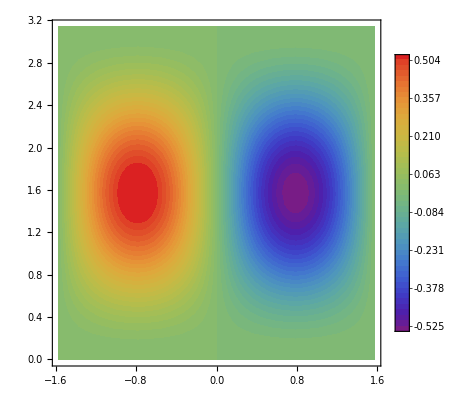

```mathematica
ContourPlot[RealSH2[2,2],{ν,-π/2,π/2},{ϕ,0,π},ColorFunction->"Rainbow",ContourLines->False,Contours->50,PlotLegends->Automatic,PlotRange->Full]
```

### Store Recursion Matrices

```mathematica
(*Recursion Matrices for the x direction*)
RecursionMatrices[N_]:=Module[{listk,recursion},

(*Loop over all the possible values of N*)
Do[
(*different values of k for this particular value of l*)
listk = Listk[ii];

(*recursion for the different values of k*)
recursion = Table[Omegamlk[ii,jj],{jj,listk}];

(*coefficient appearing in front of Subscript[m, l-1]*)
R1[ii]=CoefficientArrays[Table[jj==0,{jj,recursion}],Table[m[ii-1,jj],{jj,Listk[ii-1]}]]⟦2⟧;

(*coefficients appearingin in front of Subscript[m, l+1]*)
R2[ii]=CoefficientArrays[Table[jj==0,{jj,recursion}],Table[m[ii+1,jj],{jj,Listk[ii+1]}]]⟦2⟧;

,{ii,0,N}];


]

(*Recursion Matrices for the y direction*)
RecursionMatricesY[N_]:=Module[{listk,recursion},

(*Loop over all the possible values of N*)
Do[
(*different values of k for this particular value of l*)
listk = Listk[ii];

(*recursion for the different values of k*)
recursion = Table[OmegamlkY[ii,jj],{jj,listk}];

(*coefficient appearing in front of Subscript[m, l-1]*)
R1Y[ii]=CoefficientArrays[Table[jj==0,{jj,recursion}],Table[m[ii-1,jj],{jj,Listk[ii-1]}]]⟦2⟧;

(*coefficients appearingin in front of Subscript[m, l+1]*)
R2Y[ii]=CoefficientArrays[Table[jj==0,{jj,recursion}],Table[m[ii+1,jj],{jj,Listk[ii+1]}]]⟦2⟧;

,{ii,0,N}];


]
```

```mathematica
RecursionMatrices[40]
RecursionMatricesY[40]
```

### Position for every l

```mathematica
(*returns the total number of components in a particular Subscript[m, l]*)
positionl[N_]:=Module[{result},
Do[posl[ii]=Length[Listk[ii]];,{ii,0,N}];
]

(*returns the position of a particular Subscript[m, l] in the global flux matrix*)
positionlGlobal[N_]:=Module[{result},

(*The first component only consists of one variable. The index at which the variable starts.*)
poslGlobal[0]=1;
Do[poslGlobal[ii]=Sum[posl[jj],{jj,0,ii-1}]+1;,{ii,1,N}];
]

(*the total number of variables in the moment system = position of the last component + number of components in the last variable*)
totalVar[N_]:=((N+1)(N+2))/2;
```

```mathematica
positionl[40];
positionlGlobal[40];
```

## Projection Operator in xy plane

```mathematica
(*Projection operator for a particular value of l*)
ProjectorDegree[l_,α_]:=Module[{listk,result,numVar,nz},

listk = Listk[l];
numVar = Length[listk];
result = ConstantArray[0,{numVar,numVar}];

(*values on the diagonal*)
Do[result⟦ii,ii⟧=Cos[Abs[listk⟦ii⟧]α];,{ii,1,numVar}];

(*Half of the number of non-zero entries*)
nz = Floor[numVar/2];

Do[result⟦ii,numVar-(ii-1)⟧ = -Sin[Abs[listk⟦ii⟧]α];,{ii,1,nz}];
Do[result⟦-ii,-(numVar-(ii-1))⟧ = Sin[Abs[listk⟦ii⟧]α];,{ii,1,nz}];

result
]

(*Global projector matrix for the 2D setting*)
ProjectorGlobalSH[N_,α_]:=Module[{nEqn,result},

nEqn = totalVar[N];
result = ConstantArray[0,{nEqn,nEqn}];

Do[
result⟦poslGlobal[l];;poslGlobal[l]+posl[l]-1,poslGlobal[l];;poslGlobal[l]+posl[l]-1⟧ = ProjectorDegree[l,α];
,{l,0,N}];

result
]

InvProjectorGlobalSH[N_,α_]:=Module[{nEqn,result},
ProjectorGlobal[N,-α] 
]
```

## Half Integrals of Spherical Harmonics

#### Core Routines

```mathematica
(*Representing a product of Legendre polynomials as another Legendre polynomial*)
G[l1_,m1_,l2_,m2_,k_,m_]:=ClebschGordan[{l1,m1},{l2,m2},{k,m}]ClebschGordan[{l1,0},{l2,0},{k,0}];


(*Products of SH in terms of a single SH. *)
ProductsSH[l1_,m1_,l2_,m2_]:=Sum[√(((2l1+1)(2l2+1))/(4π(2k+1)))SphericalHarmonicY[k,m1+m2,ϕ,ν]G[l1,m1,l2,m2,k,m1+m2],{k,Max[Abs[l1-l2],Abs[m1+m2]],l1+l2}];

(*Integrate a single Associated Legendre polynomial Subscript[P, n]^m from [-1,1]*)
IntegrateLegendre[n_,m_]:=(((-1)^n+(-1)^m)/(Gamma[(n+3)/2] ((n-m)/2)!)) 2^(m-2) m Gamma[n/2] Gamma[(1/2) (n+m+1)];

(*Half Integrate a single spherical Harmonic. All values of z but only positive values of x. If m is zero then the integral is non zero only if l = 0. *)
HalfIntegrateSH[l_,m_]:=If[m ≠0,If[OddQ[m],1/m √(((2l+1)(l-m)!)/(4π(l+m)!))IntegrateLegendre[l,m](2Sin[(m π)/2]),0],KroneckerDelta[l,0] √π];

(*Integrate the Product of Spherical harmonics over a half sphere. ClebshGordon vanishes if k+m1+m2 is even. If m1 = m2, everything vanishes expect for when m1=m2=0. Then l1=l2 and only then the value is 0.5 else it is zero.*)

HalfIntegrateProductsSH[l1_,m1_,l2_,m2_]:=If[m1!=m2,Sum[If[EvenQ[k+m1+m2],N[√(((2l1+1)(2l2+1))/(4π(2k+1)))HalfIntegrateSH[k,m1+m2]G[l1,m1,l2,m2,k,m1+m2],15],0],{k,Max[Abs[l1-l2],Abs[m1+m2]],l1+l2}],If[m1==0&&l1==l2,0.5,0]];


(*coefficients which appear in real SH compact notation*)
Coeffα[m_]:=(ⅈ^Tildeθ[m](-1)^(m+Tildeθ[m]))/2^((1+KroneckerDelta[m,0])/2);

Coeffβ[m_]:=(-1)^(m+Tildeθ[m]);

(*Half integrals of real SH. The k in the Kuper's Thesis is m here.*)
HalfIntegrateProductsRealSH[l1_,m1_,l2_,m2_]:=Module[{result,α1,α2,β1,β2,int1,int2,int3,int4},

α1=Coeffα[m1];
α2 = Coeffα[m2];
β1=Coeffβ[m1];
β2 = Coeffβ[m2];

(*See the pdf for these formulaes.*)
int1 = HalfIntegrateProductsSH[l1,Abs[m1],l2,Abs[m2]];
int2 = β2 HalfIntegrateProductsSH[l1,Abs[m1],l2,-Abs[m2]];
int3 = β1 HalfIntegrateProductsSH[l1,-Abs[m1],l2,Abs[m2]];
int4 = β1 β2 HalfIntegrateProductsSH[l1,-Abs[m1],l2,-Abs[m2]];

result = α1 α2(int1 + int2 + int3+int4)

]
```

#### Testing the Integrals of Products of Spherical Harmonics

```mathematica
trialList1 = Listlk[4];
```

```mathematica
(*Test the Half Integrals of Products of Polynomials*)
testResidual2=Quiet[Table[Table[N[HalfIntegrateProductsSH[ii⟦1⟧,ii⟦2⟧,jj⟦1⟧,jj⟦2⟧]-Integrate[SphericalHarmonicY[ii⟦1⟧,ii⟦2⟧,ϕ,ν]SphericalHarmonicY[jj⟦1⟧,jj⟦2⟧,ϕ,ν]Sin[ϕ],{ϕ,0,π},{ν,-π/2,π/2}]],{jj,trialList1}],{ii,trialList1}]];
```

$Aborted

#### Testing for Generalized Formulae of Real Spherical Harmonics

```mathematica
RealSH1[l_,m_]:=If[m≠0,1/(√2)(SphericalHarmonicY[l,m,ϕ,ν]+(-1)^m SphericalHarmonicY[l,-m,ϕ,ν]),SphericalHarmonicY[l,0,ϕ,ν]];

(*m should be negative*)
RealSH2[l_,m_]:=1/(√2)(ⅈ) (SphericalHarmonicY[l,-m,ϕ,ν]-(-1)^m SphericalHarmonicY[l,m,ϕ,ν]);

GeneralRealSH[l_,m_]:=Coeffα[m](SphericalHarmonicY[l,Abs[m],ϕ,ν]+Coeffβ[m]SphericalHarmonicY[l,-Abs[m],ϕ,ν])
```

```mathematica
(*Test the generalised Real Spherical Harmonics*)
Table[Table[Simplify[GeneralRealSH[ii,jj]-RealSH2[ii,jj]],{jj,-ii,-1}],{ii,1,20}]
```

{{1/2 ⅈ ⅇ^(-ⅈ ν) (-1+ⅇ^(2 ⅈ ν)) √(3/π) Sin[ϕ]},{0,1/4 ⅈ ⅇ^(-ⅈ ν) (-1+ⅇ^(2 ⅈ ν)) √(15/π) Sin[2 ϕ]},{1/4 ⅈ ⅇ^(-3 ⅈ ν) (-1+ⅇ^(6 ⅈ ν)) √(35/(2 π)) Sin[ϕ]^3,0,1/8 ⅈ ⅇ^(-ⅈ ν) (-1+ⅇ^(2 ⅈ ν)) √(21/(2 π)) (3+5 Cos[2 ϕ]) Sin[ϕ]},{0,3/4 ⅈ ⅇ^(-3 ⅈ ν) (-1+ⅇ^(6 ⅈ ν)) √(35/(2 π)) Cos[ϕ] Sin[ϕ]^3,0,3/16 ⅈ ⅇ^(-ⅈ ν) (-1+ⅇ^(2 ⅈ ν)) √(5/(2 π)) (1+7 Cos[2 ϕ]) Sin[2 ϕ]},{3/16 ⅈ ⅇ^(-5 ⅈ ν) (-1+ⅇ^(10 ⅈ ν)) √(77/(2 π)) Sin[ϕ]^5,0,1/32 ⅈ ⅇ^(-3 ⅈ ν) (-1+ⅇ^(6 ⅈ ν)) √(385/(2 π)) (7+9 Cos[2 ϕ]) Sin[ϕ]^3,0,1/16 ⅈ ⅇ^(-ⅈ ν) (-1+ⅇ^(2 ⅈ ν)) √(165/π) (1-14 Cos[ϕ]^2+21 Cos[ϕ]^4) Sin[ϕ]},{0,3/16 ⅈ ⅇ^(-5 ⅈ ν) (-1+ⅇ^(10 ⅈ ν)) √(1001/(2 π)) Cos[ϕ] Sin[ϕ]^5,0,1/32 ⅈ ⅇ^(-3 ⅈ ν) (-1+ⅇ^(6 ⅈ ν)) √(1365/(2 π)) Cos[ϕ] (5+11 Cos[2 ϕ]) Sin[ϕ]^3,0,1/16 ⅈ ⅇ^(-ⅈ ν) (-1+ⅇ^(2 ⅈ ν)) √(273/π) Cos[ϕ] (5-30 Cos[ϕ]^2+33 Cos[ϕ]^4) Sin[ϕ]},{3/64 ⅈ ⅇ^(-7 ⅈ ν) (-1+ⅇ^(14 ⅈ ν)) √(715/π) Sin[ϕ]^7,0,3/64 ⅈ ⅇ^(-5 ⅈ ν) (-1+ⅇ^(10 ⅈ ν)) √(385/π) (-1+13 Cos[ϕ]^2) Sin[ϕ]^5,0,3/64 ⅈ ⅇ^(-3 ⅈ ν) (-1+ⅇ^(6 ⅈ ν)) √(35/π) (3-66 Cos[ϕ]^2+143 Cos[ϕ]^4) Sin[ϕ]^3,0,1/64 ⅈ ⅇ^(-ⅈ ν) (-1+ⅇ^(2 ⅈ ν)) √(105/π) (-5+135 Cos[ϕ]^2-495 Cos[ϕ]^4+429 Cos[ϕ]^6) Sin[ϕ]},{0,3/64 ⅈ ⅇ^(-7 ⅈ ν) (-1+ⅇ^(14 ⅈ ν)) √(12155/π) Cos[ϕ] Sin[ϕ]^7,0,3/128 ⅈ ⅇ^(-5 ⅈ ν) (-1+ⅇ^(10 ⅈ ν)) √(17017/π) Cos[ϕ] (3+5 Cos[2 ϕ]) Sin[ϕ]^5,0,1/64 ⅈ ⅇ^(-3 ⅈ ν) (-1+ⅇ^(6 ⅈ ν)) √(19635/π) Cos[ϕ] (3-26 Cos[ϕ]^2+39 Cos[ϕ]^4) Sin[ϕ]^3,0,(3 ⅈ ⅇ^(-ⅈ ν) (-1+ⅇ^(2 ⅈ ν)) √(17/π) (178+869 Cos[2 ϕ]+286 Cos[4 ϕ]+715 Cos[6 ϕ]) Sin[2 ϕ])/4096},{1/256 ⅈ ⅇ^(-9 ⅈ ν) (-1+ⅇ^(18 ⅈ ν)) √(230945/(2 π)) Sin[ϕ]^9,0,3/512 ⅈ ⅇ^(-7 ⅈ ν) (-1+ⅇ^(14 ⅈ ν)) √(13585/(2 π)) (15+17 Cos[2 ϕ]) Sin[ϕ]^7,0,3/128 ⅈ ⅇ^(-5 ⅈ ν) (-1+ⅇ^(10 ⅈ ν)) √(2717/(2 π)) (1-30 Cos[ϕ]^2+85 Cos[ϕ]^4) Sin[ϕ]^5,0,1/128 ⅈ ⅇ^(-3 ⅈ ν) (-1+ⅇ^(6 ⅈ ν)) √(21945/(2 π)) (-1+39 Cos[ϕ]^2-195 Cos[ϕ]^4+221 Cos[ϕ]^6) Sin[ϕ]^3,0,3/256 ⅈ ⅇ^(-ⅈ ν) (-1+ⅇ^(2 ⅈ ν)) √(95/π) (7-308 Cos[ϕ]^2+2002 Cos[ϕ]^4-4004 Cos[ϕ]^6+2431 Cos[ϕ]^8) Sin[ϕ]},{0,1/256 ⅈ ⅇ^(-9 ⅈ ν) (-1+ⅇ^(18 ⅈ ν)) √(4849845/(2 π)) Cos[ϕ] Sin[ϕ]^9,0,3/512 ⅈ ⅇ^(-7 ⅈ ν) (-1+ⅇ^(14 ⅈ ν)) √(85085/(2 π)) Cos[ϕ] (13+19 Cos[2 ϕ]) Sin[ϕ]^7,0,3/128 ⅈ ⅇ^(-5 ⅈ ν) (-1+ⅇ^(10 ⅈ ν)) √(1001/(2 π)) Cos[ϕ] (15-170 Cos[ϕ]^2+323 Cos[ϕ]^4) Sin[ϕ]^5,0,3/128 ⅈ ⅇ^(-3 ⅈ ν) (-1+ⅇ^(6 ⅈ ν)) √(5005/(2 π)) Cos[ϕ] (-7+105 Cos[ϕ]^2-357 Cos[ϕ]^4+323 Cos[ϕ]^6) Sin[ϕ]^3,0,1/256 ⅈ ⅇ^(-ⅈ ν) (-1+ⅇ^(2 ⅈ ν)) √(1155/π) Cos[ϕ] (63-1092 Cos[ϕ]^2+4914 Cos[ϕ]^4-7956 Cos[ϕ]^6+4199 Cos[ϕ]^8) Sin[ϕ]},{(ⅈ ⅇ^(-11 ⅈ ν) (-1+ⅇ^(22 ⅈ ν)) √(2028117/π) Sin[ϕ]^11)/1024,0,(ⅈ ⅇ^(-9 ⅈ ν) (-1+ⅇ^(18 ⅈ ν)) √(1062347/π) (19+21 Cos[2 ϕ]) Sin[ϕ]^9)/2048,0,(ⅈ ⅇ^(-7 ⅈ ν) (-1+ⅇ^(14 ⅈ ν)) √(838695/π) (1-38 Cos[ϕ]^2+133 Cos[ϕ]^4) Sin[ϕ]^7)/1024,0,(3 ⅈ ⅇ^(-5 ⅈ ν) (-1+ⅇ^(10 ⅈ ν)) √(3289/π) (-5+255 Cos[ϕ]^2-1615 Cos[ϕ]^4+2261 Cos[ϕ]^6) Sin[ϕ]^5)/1024,0,1/512 ⅈ ⅇ^(-3 ⅈ ν) (-1+ⅇ^(6 ⅈ ν)) √(345345/(2 π)) (1-60 Cos[ϕ]^2+510 Cos[ϕ]^4-1292 Cos[ϕ]^6+969 Cos[ϕ]^8) Sin[ϕ]^3,0,1/512 ⅈ ⅇ^(-ⅈ ν) (-1+ⅇ^(2 ⅈ ν)) √(759/(2 π)) (-21+1365 Cos[ϕ]^2-13650 Cos[ϕ]^4+46410 Cos[ϕ]^6-62985 Cos[ϕ]^8+29393 Cos[ϕ]^10) Sin[ϕ]},{0,(5 ⅈ ⅇ^(-11 ⅈ ν) (-1+ⅇ^(22 ⅈ ν)) √(2028117/π) Cos[ϕ] Sin[ϕ]^11)/1024,0,(5 ⅈ ⅇ^(-9 ⅈ ν) (-1+ⅇ^(18 ⅈ ν)) √(323323/π) Cos[ϕ] (17+23 Cos[2 ϕ]) Sin[ϕ]^9)/2048,0,(5 ⅈ ⅇ^(-7 ⅈ ν) (-1+ⅇ^(14 ⅈ ν)) √(138567/π) Cos[ϕ] (5-70 Cos[ϕ]^2+161 Cos[ϕ]^4) Sin[ϕ]^7)/1024,0,(15 ⅈ ⅇ^(-5 ⅈ ν) (-1+ⅇ^(10 ⅈ ν)) √(17017/π) Cos[ϕ] (-5+95 Cos[ϕ]^2-399 Cos[ϕ]^4+437 Cos[ϕ]^6) Sin[ϕ]^5)/1024,0,5/512 ⅈ ⅇ^(-3 ⅈ ν) (-1+ⅇ^(6 ⅈ ν)) √(1001/(2 π)) Cos[ϕ] (45-1020 Cos[ϕ]^2+5814 Cos[ϕ]^4-11628 Cos[ϕ]^6+7429 Cos[ϕ]^8) Sin[ϕ]^3,0,5/512 ⅈ ⅇ^(-ⅈ ν) (-1+ⅇ^(2 ⅈ ν)) √(39/(2 π)) Cos[ϕ] (-231+5775 Cos[ϕ]^2-39270 Cos[ϕ]^4+106590 Cos[ϕ]^6-124355 Cos[ϕ]^8+52003 Cos[ϕ]^10) Sin[ϕ]},{(15 ⅈ ⅇ^(-13 ⅈ ν) (-1+ⅇ^(26 ⅈ ν)) √(156009/π) Sin[ϕ]^13)/4096,0,(3 ⅈ ⅇ^(-11 ⅈ ν) (-1+ⅇ^(22 ⅈ ν)) √(2028117/π) (23+25 Cos[2 ϕ]) Sin[ϕ]^11)/8192,0,(3 ⅈ ⅇ^(-9 ⅈ ν) (-1+ⅇ^(18 ⅈ ν)) √(88179/(2 π)) (3-138 Cos[ϕ]^2+575 Cos[ϕ]^4) Sin[ϕ]^9)/2048,0,(3 ⅈ ⅇ^(-7 ⅈ ν) (-1+ⅇ^(14 ⅈ ν)) √(692835/(2 π)) (-1+63 Cos[ϕ]^2-483 Cos[ϕ]^4+805 Cos[ϕ]^6) Sin[ϕ]^7)/2048,0,(3 ⅈ ⅇ^(-5 ⅈ ν) (-1+ⅇ^(10 ⅈ ν)) √(51051/π) (5-380 Cos[ϕ]^2+3990 Cos[ϕ]^4-12236 Cos[ϕ]^6+10925 Cos[ϕ]^8) Sin[ϕ]^5)/4096,0,(3 ⅈ ⅇ^(-3 ⅈ ν) (-1+ⅇ^(6 ⅈ ν)) √(15015/π) (-9+765 Cos[ϕ]^2-9690 Cos[ϕ]^4+40698 Cos[ϕ]^6-66861 Cos[ϕ]^8+37145 Cos[ϕ]^10) Sin[ϕ]^3)/4096,0,1/2048 3 ⅈ ⅇ^(-ⅈ ν) (-1+ⅇ^(2 ⅈ ν)) √(273/π) (33-2970 Cos[ϕ]^2+42075 Cos[ϕ]^4-213180 Cos[ϕ]^6+479655 Cos[ϕ]^8-490314 Cos[ϕ]^10+185725 Cos[ϕ]^12) Sin[ϕ]},{0,(15 ⅈ ⅇ^(-13 ⅈ ν) (-1+ⅇ^(26 ⅈ ν)) √(4524261/π) Cos[ϕ] Sin[ϕ]^13)/4096,0,(5 ⅈ ⅇ^(-11 ⅈ ν) (-1+ⅇ^(22 ⅈ ν)) √(58815393/π) Cos[ϕ] (7+9 Cos[2 ϕ]) Sin[ϕ]^11)/8192,0,(ⅈ ⅇ^(-9 ⅈ ν) (-1+ⅇ^(18 ⅈ ν)) √(98025655/(2 π)) Cos[ϕ] (3-50 Cos[ϕ]^2+135 Cos[ϕ]^4) Sin[ϕ]^9)/2048,0,(ⅈ ⅇ^(-7 ⅈ ν) (-1+ⅇ^(14 ⅈ ν)) √(20092215/(2 π)) Cos[ϕ] (-7+161 Cos[ϕ]^2-805 Cos[ϕ]^4+1035 Cos[ϕ]^6) Sin[ϕ]^7)/2048,0,(3 ⅈ ⅇ^(-5 ⅈ ν) (-1+ⅇ^(10 ⅈ ν)) √(9376367/π) Cos[ϕ] (5-140 Cos[ϕ]^2+966 Cos[ϕ]^4-2300 Cos[ϕ]^6+1725 Cos[ϕ]^8) Sin[ϕ]^5)/4096,0,1/4096 ⅈ ⅇ^(-3 ⅈ ν) (-1+ⅇ^(6 ⅈ ν)) √(224315/π) Cos[ϕ] (-99+3135 Cos[ϕ]^2-26334 Cos[ϕ]^4+86526 Cos[ϕ]^6-120175 Cos[ϕ]^8+58995 Cos[ϕ]^10) Sin[ϕ]^3,0,1/2048 ⅈ ⅇ^(-ⅈ ν) (-1+ⅇ^(2 ⅈ ν)) √(3045/π) Cos[ϕ] (429-14586 Cos[ϕ]^2+138567 Cos[ϕ]^4-554268 Cos[ϕ]^6+1062347 Cos[ϕ]^8-965770 Cos[ϕ]^10+334305 Cos[ϕ]^12) Sin[ϕ]},{(3 ⅈ ⅇ^(-15 ⅈ ν) (-1+ⅇ^(30 ⅈ ν)) √(33393355/(2 π)) Sin[ϕ]^15)/8192,0,(15 ⅈ ⅇ^(-13 ⅈ ν) (-1+ⅇ^(26 ⅈ ν)) √(690897/(2 π)) (-1+29 Cos[ϕ]^2) Sin[ϕ]^13)/8192,0,(5 ⅈ ⅇ^(-11 ⅈ ν) (-1+ⅇ^(22 ⅈ ν)) √(4836279/(2 π)) (1-54 Cos[ϕ]^2+261 Cos[ϕ]^4) Sin[ϕ]^11)/8192,0,(ⅈ ⅇ^(-9 ⅈ ν) (-1+ⅇ^(18 ⅈ ν)) √(104786045/(2 π)) (-1+75 Cos[ϕ]^2-675 Cos[ϕ]^4+1305 Cos[ϕ]^6) Sin[ϕ]^9)/8192,0,(ⅈ ⅇ^(-7 ⅈ ν) (-1+ⅇ^(14 ⅈ ν)) √(1952535/(2 π)) (7-644 Cos[ϕ]^2+8050 Cos[ϕ]^4-28980 Cos[ϕ]^6+30015 Cos[ϕ]^8) Sin[ϕ]^7)/8192,0,(3 ⅈ ⅇ^(-5 ⅈ ν) (-1+ⅇ^(10 ⅈ ν)) √(10023013/(2 π)) (-1+105 Cos[ϕ]^2-1610 Cos[ϕ]^4+8050 Cos[ϕ]^6-15525 Cos[ϕ]^8+10005 Cos[ϕ]^10) Sin[ϕ]^5)/8192,0,1/8192 ⅈ ⅇ^(-3 ⅈ ν) (-1+ⅇ^(6 ⅈ ν)) √(719355/(2 π)) (11-1254 Cos[ϕ]^2+21945 Cos[ϕ]^4-134596 Cos[ϕ]^6+360525 Cos[ϕ]^8-432630 Cos[ϕ]^10+190095 Cos[ϕ]^12) Sin[ϕ]^3,0,1/8192 ⅈ ⅇ^(-ⅈ ν) (-1+ⅇ^(2 ⅈ ν)) √(465/(2 π)) (-429+51051 Cos[ϕ]^2-969969 Cos[ϕ]^4+6789783 Cos[ϕ]^6-22309287 Cos[ϕ]^8+37182145 Cos[ϕ]^10-30421755 Cos[ϕ]^12+9694845 Cos[ϕ]^14) Sin[ϕ]},{0,(3 ⅈ ⅇ^(-15 ⅈ ν) (-1+ⅇ^(30 ⅈ ν)) √(1101980715/(2 π)) Cos[ϕ] Sin[ϕ]^15)/8192,0,(15 ⅈ ⅇ^(-13 ⅈ ν) (-1+ⅇ^(26 ⅈ ν)) √(7109553/(2 π)) Cos[ϕ] (-3+31 Cos[ϕ]^2) Sin[ϕ]^13)/8192,0,(3 ⅈ ⅇ^(-11 ⅈ ν) (-1+ⅇ^(22 ⅈ ν)) √(8580495/(2 π)) Cos[ϕ] (15-290 Cos[ϕ]^2+899 Cos[ϕ]^4) Sin[ϕ]^11)/8192,0,(ⅈ ⅇ^(-9 ⅈ ν) (-1+ⅇ^(18 ⅈ ν)) √(15935205/(2 π)) Cos[ϕ] (-35+945 Cos[ϕ]^2-5481 Cos[ϕ]^4+8091 Cos[ϕ]^6) Sin[ϕ]^9)/8192,0,(3 ⅈ ⅇ^(-7 ⅈ ν) (-1+ⅇ^(14 ⅈ ν)) √(5311735/(2 π)) Cos[ϕ] (21-700 Cos[ϕ]^2+5670 Cos[ϕ]^4-15660 Cos[ϕ]^6+13485 Cos[ϕ]^8) Sin[ϕ]^7)/8192,0,1/8192 3 ⅈ ⅇ^(-5 ⅈ ν) (-1+ⅇ^(10 ⅈ ν)) √(46189/(2 π)) Cos[ϕ] (-231+8855 Cos[ϕ]^2-88550 Cos[ϕ]^4+341550 Cos[ϕ]^6-550275 Cos[ϕ]^8+310155 Cos[ϕ]^10) Sin[ϕ]^5,0,1/8192 3 ⅈ ⅇ^(-3 ⅈ ν) (-1+ⅇ^(6 ⅈ ν)) √(124355/(2 π)) Cos[ϕ] (143-6006 Cos[ϕ]^2+69069 Cos[ϕ]^4-328900 Cos[ϕ]^6+740025 Cos[ϕ]^8-780390 Cos[ϕ]^10+310155 Cos[ϕ]^12) Sin[ϕ]^3,0,1/8192 ⅈ ⅇ^(-ⅈ ν) (-1+ⅇ^(2 ⅈ ν)) √(561/(2 π)) Cos[ϕ] (-6435+285285 Cos[ϕ]^2-3594591 Cos[ϕ]^4+19684665 Cos[ϕ]^6-54679625 Cos[ϕ]^8+80528175 Cos[ϕ]^10-59879925 Cos[ϕ]^12+17678835 Cos[ϕ]^14) Sin[ϕ]},{(15 ⅈ ⅇ^(-17 ⅈ ν) (-1+ⅇ^(34 ⅈ ν)) √(90751353/(2 π)) Sin[ϕ]^17)/65536,0,(15 ⅈ ⅇ^(-15 ⅈ ν) (-1+ⅇ^(30 ⅈ ν)) √(46750697/(2 π)) (-1+33 Cos[ϕ]^2) Sin[ϕ]^15)/65536,0,(15 ⅈ ⅇ^(-13 ⅈ ν) (-1+ⅇ^(26 ⅈ ν)) √(4524261/π) (1-62 Cos[ϕ]^2+341 Cos[ϕ]^4) Sin[ϕ]^13)/32768,0,(15 ⅈ ⅇ^(-11 ⅈ ν) (-1+ⅇ^(22 ⅈ ν)) √(156009/π) (-5+435 Cos[ϕ]^2-4495 Cos[ϕ]^4+9889 Cos[ϕ]^6) Sin[ϕ]^11)/32768,0,(5 ⅈ ⅇ^(-9 ⅈ ν) (-1+ⅇ^(18 ⅈ ν)) √(52003/(2 π)) (35-3780 Cos[ϕ]^2+54810 Cos[ϕ]^4-226548 Cos[ϕ]^6+267003 Cos[ϕ]^8) Sin[ϕ]^9)/32768,0,1/32768 3 ⅈ ⅇ^(-7 ⅈ ν) (-1+ⅇ^(14 ⅈ ν)) √(3380195/(2 π)) (-7+875 Cos[ϕ]^2-15750 Cos[ϕ]^4+91350 Cos[ϕ]^6-202275 Cos[ϕ]^8+148335 Cos[ϕ]^10) Sin[ϕ]^7,0,1/32768 3 ⅈ ⅇ^(-5 ⅈ ν) (-1+ⅇ^(10 ⅈ ν)) √(1616615/π) (7-966 Cos[ϕ]^2+20125 Cos[ϕ]^4-144900 Cos[ϕ]^6+450225 Cos[ϕ]^8-620310 Cos[ϕ]^10+310155 Cos[ϕ]^12) Sin[ϕ]^5,0,1/32768 ⅈ ⅇ^(-3 ⅈ ν) (-1+ⅇ^(6 ⅈ ν)) √(33915/π) (-143+21021 Cos[ϕ]^2-483483 Cos[ϕ]^4+4029025 Cos[ϕ]^6-15540525 Cos[ϕ]^8+30045015 Cos[ϕ]^10-28224105 Cos[ϕ]^12+10235115 Cos[ϕ]^14) Sin[ϕ]^3,0,1/65536 3 ⅈ ⅇ^(-ⅈ ν) (-1+ⅇ^(2 ⅈ ν)) √(595/π) (715-108680 Cos[ϕ]^2+2662660 Cos[ϕ]^4-24496472 Cos[ϕ]^6+109359250 Cos[ϕ]^8-262462200 Cos[ϕ]^10+345972900 Cos[ϕ]^12-235717800 Cos[ϕ]^14+64822395 Cos[ϕ]^16) Sin[ϕ]},{0,(15 ⅈ ⅇ^(-17 ⅈ ν) (-1+ⅇ^(34 ⅈ ν)) √(3357800061/(2 π)) Cos[ϕ] Sin[ϕ]^17)/65536,0,(3 ⅈ ⅇ^(-15 ⅈ ν) (-1+ⅇ^(30 ⅈ ν)) √(13591095485/(2 π)) Cos[ϕ] (-3+35 Cos[ϕ]^2) Sin[ϕ]^15)/65536,0,(15 ⅈ ⅇ^(-13 ⅈ ν) (-1+ⅇ^(26 ⅈ ν)) √(741332481/π) Cos[ϕ] (1-22 Cos[ϕ]^2+77 Cos[ϕ]^4) Sin[ϕ]^13)/32768,0,(3 ⅈ ⅇ^(-11 ⅈ ν) (-1+ⅇ^(22 ⅈ ν)) √(836988285/π) Cos[ϕ] (-5+155 Cos[ϕ]^2-1023 Cos[ϕ]^4+1705 Cos[ϕ]^6) Sin[ϕ]^11)/32768,0,(ⅈ ⅇ^(-9 ⅈ ν) (-1+ⅇ^(18 ⅈ ν)) √(4123095/(2 π)) Cos[ϕ] (315-12180 Cos[ϕ]^2+113274 Cos[ϕ]^4-356004 Cos[ϕ]^6+346115 Cos[ϕ]^8) Sin[ϕ]^9)/32768,0,1/32768 15 ⅈ ⅇ^(-7 ⅈ ν) (-1+ⅇ^(14 ⅈ ν)) √(39306839/(2 π)) Cos[ϕ] (-7+315 Cos[ϕ]^2-3654 Cos[ϕ]^4+16182 Cos[ϕ]^6-29667 Cos[ϕ]^8+18879 Cos[ϕ]^10) Sin[ϕ]^7,0,1/32768 3 ⅈ ⅇ^(-5 ⅈ ν) (-1+ⅇ^(10 ⅈ ν)) √(3023603/π) Cos[ϕ] (91-4550 Cos[ϕ]^2+61425 Cos[ϕ]^4-339300 Cos[ϕ]^6+876525 Cos[ϕ]^8-1051830 Cos[ϕ]^10+471975 Cos[ϕ]^12) Sin[ϕ]^5,0,1/32768 ⅈ ⅇ^(-3 ⅈ ν) (-1+ⅇ^(6 ⅈ ν)) √(1254855/π) Cos[ϕ] (-429+23023 Cos[ϕ]^2-345345 Cos[ϕ]^4+2220075 Cos[ϕ]^6-7153575 Cos[ϕ]^8+12096045 Cos[ϕ]^10-10235115 Cos[ϕ]^12+3411705 Cos[ϕ]^14) Sin[ϕ]^3,0,1/65536 3 ⅈ ⅇ^(-ⅈ ν) (-1+ⅇ^(2 ⅈ ν)) √(703/π) Cos[ϕ] (12155-680680 Cos[ϕ]^2+10958948 Cos[ϕ]^4-78278200 Cos[ϕ]^6+293543250 Cos[ϕ]^8-619109400 Cos[ϕ]^10+738168900 Cos[ϕ]^12-463991880 Cos[ϕ]^14+119409675 Cos[ϕ]^16) Sin[ϕ]},{(15 ⅈ ⅇ^(-19 ⅈ ν) (-1+ⅇ^(38 ⅈ ν)) √(765814049/π) Sin[ϕ]^19)/262144,0,(15 ⅈ ⅇ^(-17 ⅈ ν) (-1+ⅇ^(34 ⅈ ν)) √(393255863/π) (35+37 Cos[2 ϕ]) Sin[ϕ]^17)/524288,0,(3 ⅈ ⅇ^(-15 ⅈ ν) (-1+ⅇ^(30 ⅈ ν)) √(842691135/π) (3-210 Cos[ϕ]^2+1295 Cos[ϕ]^4) Sin[ϕ]^15)/262144,0,(15 ⅈ ⅇ^(-13 ⅈ ν) (-1+ⅇ^(26 ⅈ ν)) √(260468169/π) (-1+99 Cos[ϕ]^2-1155 Cos[ϕ]^4+2849 Cos[ϕ]^6) Sin[ϕ]^13)/262144,0,(15 ⅈ ⅇ^(-11 ⅈ ν) (-1+ⅇ^(22 ⅈ ν)) √(58815393/π) (1-124 Cos[ϕ]^2+2046 Cos[ϕ]^4-9548 Cos[ϕ]^6+12617 Cos[ϕ]^8) Sin[ϕ]^11)/131072,0,1/131072 15 ⅈ ⅇ^(-9 ⅈ ν) (-1+ⅇ^(18 ⅈ ν)) √(676039/π) (-9+1305 Cos[ϕ]^2-26970 Cos[ϕ]^4+178002 Cos[ϕ]^6-445005 Cos[ϕ]^8+365893 Cos[ϕ]^10) Sin[ϕ]^9,0,1/131072 15 ⅈ ⅇ^(-7 ⅈ ν) (-1+ⅇ^(14 ⅈ ν)) √(1062347/π) (7-1134 Cos[ϕ]^2+27405 Cos[ϕ]^4-226548 Cos[ϕ]^6+801009 Cos[ϕ]^8-1246014 Cos[ϕ]^10+698523 Cos[ϕ]^12) Sin[ϕ]^7,0,1/131072 3 ⅈ ⅇ^(-5 ⅈ ν) (-1+ⅇ^(10 ⅈ ν)) √(7436429/π) (-13+2275 Cos[ϕ]^2-61425 Cos[ϕ]^4+593775 Cos[ϕ]^6-2629575 Cos[ϕ]^8+5785065 Cos[ϕ]^10-6135675 Cos[ϕ]^12+2494725 Cos[ϕ]^14) Sin[ϕ]^5,0,1/131072 3 ⅈ ⅇ^(-3 ⅈ ν) (-1+ⅇ^(6 ⅈ ν)) √(1616615/(2 π)) (39-7176 Cos[ϕ]^2+209300 Cos[ϕ]^4-2260440 Cos[ϕ]^6+11705850 Cos[ϕ]^8-32256120 Cos[ϕ]^10+48384180 Cos[ϕ]^12-37218600 Cos[ϕ]^14+11475735 Cos[ϕ]^16) Sin[ϕ]^3,0,1/131072 ⅈ ⅇ^(-ⅈ ν) (-1+ⅇ^(2 ⅈ ν)) √(3705/(2 π)) (-2431+459459 Cos[ϕ]^2-14090076 Cos[ϕ]^4+164384220 Cos[ϕ]^6-951080130 Cos[ϕ]^8+3064591530 Cos[ϕ]^10-5757717420 Cos[ϕ]^12+6263890380 Cos[ϕ]^14-3653936055 Cos[ϕ]^16+883631595 Cos[ϕ]^18) Sin[ϕ]},{0,(15 ⅈ ⅇ^(-19 ⅈ ν) (-1+ⅇ^(38 ⅈ ν)) √(31398376009/π) Cos[ϕ] Sin[ϕ]^19)/262144,0,(15 ⅈ ⅇ^(-17 ⅈ ν) (-1+ⅇ^(34 ⅈ ν)) √(45889934167/π) Cos[ϕ] (11+13 Cos[2 ϕ]) Sin[ϕ]^17)/524288,0,(3 ⅈ ⅇ^(-15 ⅈ ν) (-1+ⅇ^(30 ⅈ ν)) √(6201342455/π) Cos[ϕ] (15-370 Cos[ϕ]^2+1443 Cos[ϕ]^4) Sin[ϕ]^15)/262144,0,(15 ⅈ ⅇ^(-13 ⅈ ν) (-1+ⅇ^(26 ⅈ ν)) √(63253693041/π) Cos[ϕ] (-1+35 Cos[ϕ]^2-259 Cos[ϕ]^4+481 Cos[ϕ]^6) Sin[ϕ]^13)/262144,0,(15 ⅈ ⅇ^(-11 ⅈ ν) (-1+ⅇ^(22 ⅈ ν)) √(1916778577/π) Cos[ϕ] (3-132 Cos[ϕ]^2+1386 Cos[ϕ]^4-4884 Cos[ϕ]^6+5291 Cos[ϕ]^8) Sin[ϕ]^11)/131072,0,1/131072 5 ⅈ ⅇ^(-9 ⅈ ν) (-1+ⅇ^(18 ⅈ ν)) √(2040441711/π) Cos[ϕ] (-9+465 Cos[ϕ]^2-6138 Cos[ϕ]^4+30690 Cos[ϕ]^6-63085 Cos[ϕ]^8+44733 Cos[ϕ]^10) Sin[ϕ]^9,0,1/131072 15 ⅈ ⅇ^(-7 ⅈ ν) (-1+ⅇ^(14 ⅈ ν)) √(43556227/π) Cos[ϕ] (21-1218 Cos[ϕ]^2+18879 Cos[ϕ]^4-118668 Cos[ϕ]^6+346115 Cos[ϕ]^8-465682 Cos[ϕ]^10+232841 Cos[ϕ]^12) Sin[ϕ]^7,0,1/131072 3 ⅈ ⅇ^(-5 ⅈ ν) (-1+ⅇ^(10 ⅈ ν)) √(117266765/π) Cos[ϕ] (-65+4095 Cos[ϕ]^2-71253 Cos[ϕ]^4+525915 Cos[ϕ]^6-1928355 Cos[ϕ]^8+3681405 Cos[ϕ]^10-3492615 Cos[ϕ]^12+1297257 Cos[ϕ]^14) Sin[ϕ]^5,0,1/131072 ⅈ ⅇ^(-3 ⅈ ν) (-1+ⅇ^(6 ⅈ ν)) √(20694135/(2 π)) Cos[ϕ] (663-44200 Cos[ϕ]^2+835380 Cos[ϕ]^4-6921720 Cos[ϕ]^6+29801850 Cos[ϕ]^8-71524440 Cos[ϕ]^10+96282900 Cos[ϕ]^12-67856520 Cos[ϕ]^14+19458855 Cos[ϕ]^16) Sin[ϕ]^3,0,1/131072 ⅈ ⅇ^(-ⅈ ν) (-1+ⅇ^(2 ⅈ ν)) √(4305/(2 π)) Cos[ϕ] (-46189+3187041 Cos[ϕ]^2-63740820 Cos[ϕ]^4+573667380 Cos[ϕ]^6-2772725670 Cos[ϕ]^8+7814045070 Cos[ϕ]^10-13223768580 Cos[ϕ]^12+13223768580 Cos[ϕ]^14-7195285845 Cos[ϕ]^16+1641030105 Cos[ϕ]^18) Sin[ϕ]}}

```mathematica
Table[Table[Simplify[GeneralRealSH[ii,jj]-RealSH1[ii,jj]],{jj,0,ii}],{ii,1,20}]
```

{{0,1/2 ⅇ^(-ⅈ ν) (1+ⅇ^(2 ⅈ ν)) √(3/π) Sin[ϕ]},{0,1/4 ⅇ^(-ⅈ ν) (1+ⅇ^(2 ⅈ ν)) √(15/π) Sin[2 ϕ],0},{0,1/8 ⅇ^(-ⅈ ν) (1+ⅇ^(2 ⅈ ν)) √(21/(2 π)) (3+5 Cos[2 ϕ]) Sin[ϕ],0,1/4 ⅇ^(-3 ⅈ ν) (1+ⅇ^(6 ⅈ ν)) √(35/(2 π)) Sin[ϕ]^3},{0,3/16 ⅇ^(-ⅈ ν) (1+ⅇ^(2 ⅈ ν)) √(5/(2 π)) (1+7 Cos[2 ϕ]) Sin[2 ϕ],0,3/4 ⅇ^(-3 ⅈ ν) (1+ⅇ^(6 ⅈ ν)) √(35/(2 π)) Cos[ϕ] Sin[ϕ]^3,0},{0,1/16 ⅇ^(-ⅈ ν) (1+ⅇ^(2 ⅈ ν)) √(165/π) (1-14 Cos[ϕ]^2+21 Cos[ϕ]^4) Sin[ϕ],0,1/32 ⅇ^(-3 ⅈ ν) (1+ⅇ^(6 ⅈ ν)) √(385/(2 π)) (7+9 Cos[2 ϕ]) Sin[ϕ]^3,0,3/16 ⅇ^(-5 ⅈ ν) (1+ⅇ^(10 ⅈ ν)) √(77/(2 π)) Sin[ϕ]^5},{0,1/16 ⅇ^(-ⅈ ν) (1+ⅇ^(2 ⅈ ν)) √(273/π) Cos[ϕ] (5-30 Cos[ϕ]^2+33 Cos[ϕ]^4) Sin[ϕ],0,1/32 ⅇ^(-3 ⅈ ν) (1+ⅇ^(6 ⅈ ν)) √(1365/(2 π)) Cos[ϕ] (5+11 Cos[2 ϕ]) Sin[ϕ]^3,0,3/16 ⅇ^(-5 ⅈ ν) (1+ⅇ^(10 ⅈ ν)) √(1001/(2 π)) Cos[ϕ] Sin[ϕ]^5,0},{0,1/64 ⅇ^(-ⅈ ν) (1+ⅇ^(2 ⅈ ν)) √(105/π) (-5+135 Cos[ϕ]^2-495 Cos[ϕ]^4+429 Cos[ϕ]^6) Sin[ϕ],0,3/64 ⅇ^(-3 ⅈ ν) (1+ⅇ^(6 ⅈ ν)) √(35/π) (3-66 Cos[ϕ]^2+143 Cos[ϕ]^4) Sin[ϕ]^3,0,3/64 ⅇ^(-5 ⅈ ν) (1+ⅇ^(10 ⅈ ν)) √(385/π) (-1+13 Cos[ϕ]^2) Sin[ϕ]^5,0,3/64 ⅇ^(-7 ⅈ ν) (1+ⅇ^(14 ⅈ ν)) √(715/π) Sin[ϕ]^7},{0,(3 ⅇ^(-ⅈ ν) (1+ⅇ^(2 ⅈ ν)) √(17/π) (178+869 Cos[2 ϕ]+286 Cos[4 ϕ]+715 Cos[6 ϕ]) Sin[2 ϕ])/4096,0,1/64 ⅇ^(-3 ⅈ ν) (1+ⅇ^(6 ⅈ ν)) √(19635/π) Cos[ϕ] (3-26 Cos[ϕ]^2+39 Cos[ϕ]^4) Sin[ϕ]^3,0,3/128 ⅇ^(-5 ⅈ ν) (1+ⅇ^(10 ⅈ ν)) √(17017/π) Cos[ϕ] (3+5 Cos[2 ϕ]) Sin[ϕ]^5,0,3/64 ⅇ^(-7 ⅈ ν) (1+ⅇ^(14 ⅈ ν)) √(12155/π) Cos[ϕ] Sin[ϕ]^7,0},{0,3/256 ⅇ^(-ⅈ ν) (1+ⅇ^(2 ⅈ ν)) √(95/π) (7-308 Cos[ϕ]^2+2002 Cos[ϕ]^4-4004 Cos[ϕ]^6+2431 Cos[ϕ]^8) Sin[ϕ],0,1/128 ⅇ^(-3 ⅈ ν) (1+ⅇ^(6 ⅈ ν)) √(21945/(2 π)) (-1+39 Cos[ϕ]^2-195 Cos[ϕ]^4+221 Cos[ϕ]^6) Sin[ϕ]^3,0,3/128 ⅇ^(-5 ⅈ ν) (1+ⅇ^(10 ⅈ ν)) √(2717/(2 π)) (1-30 Cos[ϕ]^2+85 Cos[ϕ]^4) Sin[ϕ]^5,0,3/512 ⅇ^(-7 ⅈ ν) (1+ⅇ^(14 ⅈ ν)) √(13585/(2 π)) (15+17 Cos[2 ϕ]) Sin[ϕ]^7,0,1/256 ⅇ^(-9 ⅈ ν) (1+ⅇ^(18 ⅈ ν)) √(230945/(2 π)) Sin[ϕ]^9},{0,1/256 ⅇ^(-ⅈ ν) (1+ⅇ^(2 ⅈ ν)) √(1155/π) Cos[ϕ] (63-1092 Cos[ϕ]^2+4914 Cos[ϕ]^4-7956 Cos[ϕ]^6+4199 Cos[ϕ]^8) Sin[ϕ],0,3/128 ⅇ^(-3 ⅈ ν) (1+ⅇ^(6 ⅈ ν)) √(5005/(2 π)) Cos[ϕ] (-7+105 Cos[ϕ]^2-357 Cos[ϕ]^4+323 Cos[ϕ]^6) Sin[ϕ]^3,0,3/128 ⅇ^(-5 ⅈ ν) (1+ⅇ^(10 ⅈ ν)) √(1001/(2 π)) Cos[ϕ] (15-170 Cos[ϕ]^2+323 Cos[ϕ]^4) Sin[ϕ]^5,0,3/512 ⅇ^(-7 ⅈ ν) (1+ⅇ^(14 ⅈ ν)) √(85085/(2 π)) Cos[ϕ] (13+19 Cos[2 ϕ]) Sin[ϕ]^7,0,1/256 ⅇ^(-9 ⅈ ν) (1+ⅇ^(18 ⅈ ν)) √(4849845/(2 π)) Cos[ϕ] Sin[ϕ]^9,0},{0,1/512 ⅇ^(-ⅈ ν) (1+ⅇ^(2 ⅈ ν)) √(759/(2 π)) (-21+1365 Cos[ϕ]^2-13650 Cos[ϕ]^4+46410 Cos[ϕ]^6-62985 Cos[ϕ]^8+29393 Cos[ϕ]^10) Sin[ϕ],0,1/512 ⅇ^(-3 ⅈ ν) (1+ⅇ^(6 ⅈ ν)) √(345345/(2 π)) (1-60 Cos[ϕ]^2+510 Cos[ϕ]^4-1292 Cos[ϕ]^6+969 Cos[ϕ]^8) Sin[ϕ]^3,0,(3 ⅇ^(-5 ⅈ ν) (1+ⅇ^(10 ⅈ ν)) √(3289/π) (-5+255 Cos[ϕ]^2-1615 Cos[ϕ]^4+2261 Cos[ϕ]^6) Sin[ϕ]^5)/1024,0,(ⅇ^(-7 ⅈ ν) (1+ⅇ^(14 ⅈ ν)) √(838695/π) (1-38 Cos[ϕ]^2+133 Cos[ϕ]^4) Sin[ϕ]^7)/1024,0,(ⅇ^(-9 ⅈ ν) (1+ⅇ^(18 ⅈ ν)) √(1062347/π) (19+21 Cos[2 ϕ]) Sin[ϕ]^9)/2048,0,(ⅇ^(-11 ⅈ ν) (1+ⅇ^(22 ⅈ ν)) √(2028117/π) Sin[ϕ]^11)/1024},{0,5/512 ⅇ^(-ⅈ ν) (1+ⅇ^(2 ⅈ ν)) √(39/(2 π)) Cos[ϕ] (-231+5775 Cos[ϕ]^2-39270 Cos[ϕ]^4+106590 Cos[ϕ]^6-124355 Cos[ϕ]^8+52003 Cos[ϕ]^10) Sin[ϕ],0,5/512 ⅇ^(-3 ⅈ ν) (1+ⅇ^(6 ⅈ ν)) √(1001/(2 π)) Cos[ϕ] (45-1020 Cos[ϕ]^2+5814 Cos[ϕ]^4-11628 Cos[ϕ]^6+7429 Cos[ϕ]^8) Sin[ϕ]^3,0,(15 ⅇ^(-5 ⅈ ν) (1+ⅇ^(10 ⅈ ν)) √(17017/π) Cos[ϕ] (-5+95 Cos[ϕ]^2-399 Cos[ϕ]^4+437 Cos[ϕ]^6) Sin[ϕ]^5)/1024,0,(5 ⅇ^(-7 ⅈ ν) (1+ⅇ^(14 ⅈ ν)) √(138567/π) Cos[ϕ] (5-70 Cos[ϕ]^2+161 Cos[ϕ]^4) Sin[ϕ]^7)/1024,0,(5 ⅇ^(-9 ⅈ ν) (1+ⅇ^(18 ⅈ ν)) √(323323/π) Cos[ϕ] (17+23 Cos[2 ϕ]) Sin[ϕ]^9)/2048,0,(5 ⅇ^(-11 ⅈ ν) (1+ⅇ^(22 ⅈ ν)) √(2028117/π) Cos[ϕ] Sin[ϕ]^11)/1024,0},{0,1/2048 3 ⅇ^(-ⅈ ν) (1+ⅇ^(2 ⅈ ν)) √(273/π) (33-2970 Cos[ϕ]^2+42075 Cos[ϕ]^4-213180 Cos[ϕ]^6+479655 Cos[ϕ]^8-490314 Cos[ϕ]^10+185725 Cos[ϕ]^12) Sin[ϕ],0,(3 ⅇ^(-3 ⅈ ν) (1+ⅇ^(6 ⅈ ν)) √(15015/π) (-9+765 Cos[ϕ]^2-9690 Cos[ϕ]^4+40698 Cos[ϕ]^6-66861 Cos[ϕ]^8+37145 Cos[ϕ]^10) Sin[ϕ]^3)/4096,0,(3 ⅇ^(-5 ⅈ ν) (1+ⅇ^(10 ⅈ ν)) √(51051/π) (5-380 Cos[ϕ]^2+3990 Cos[ϕ]^4-12236 Cos[ϕ]^6+10925 Cos[ϕ]^8) Sin[ϕ]^5)/4096,0,(3 ⅇ^(-7 ⅈ ν) (1+ⅇ^(14 ⅈ ν)) √(692835/(2 π)) (-1+63 Cos[ϕ]^2-483 Cos[ϕ]^4+805 Cos[ϕ]^6) Sin[ϕ]^7)/2048,0,(3 ⅇ^(-9 ⅈ ν) (1+ⅇ^(18 ⅈ ν)) √(88179/(2 π)) (3-138 Cos[ϕ]^2+575 Cos[ϕ]^4) Sin[ϕ]^9)/2048,0,(3 ⅇ^(-11 ⅈ ν) (1+ⅇ^(22 ⅈ ν)) √(2028117/π) (23+25 Cos[2 ϕ]) Sin[ϕ]^11)/8192,0,(15 ⅇ^(-13 ⅈ ν) (1+ⅇ^(26 ⅈ ν)) √(156009/π) Sin[ϕ]^13)/4096},{0,1/2048 ⅇ^(-ⅈ ν) (1+ⅇ^(2 ⅈ ν)) √(3045/π) Cos[ϕ] (429-14586 Cos[ϕ]^2+138567 Cos[ϕ]^4-554268 Cos[ϕ]^6+1062347 Cos[ϕ]^8-965770 Cos[ϕ]^10+334305 Cos[ϕ]^12) Sin[ϕ],0,1/4096 ⅇ^(-3 ⅈ ν) (1+ⅇ^(6 ⅈ ν)) √(224315/π) Cos[ϕ] (-99+3135 Cos[ϕ]^2-26334 Cos[ϕ]^4+86526 Cos[ϕ]^6-120175 Cos[ϕ]^8+58995 Cos[ϕ]^10) Sin[ϕ]^3,0,(3 ⅇ^(-5 ⅈ ν) (1+ⅇ^(10 ⅈ ν)) √(9376367/π) Cos[ϕ] (5-140 Cos[ϕ]^2+966 Cos[ϕ]^4-2300 Cos[ϕ]^6+1725 Cos[ϕ]^8) Sin[ϕ]^5)/4096,0,(ⅇ^(-7 ⅈ ν) (1+ⅇ^(14 ⅈ ν)) √(20092215/(2 π)) Cos[ϕ] (-7+161 Cos[ϕ]^2-805 Cos[ϕ]^4+1035 Cos[ϕ]^6) Sin[ϕ]^7)/2048,0,(ⅇ^(-9 ⅈ ν) (1+ⅇ^(18 ⅈ ν)) √(98025655/(2 π)) Cos[ϕ] (3-50 Cos[ϕ]^2+135 Cos[ϕ]^4) Sin[ϕ]^9)/2048,0,(5 ⅇ^(-11 ⅈ ν) (1+ⅇ^(22 ⅈ ν)) √(58815393/π) Cos[ϕ] (7+9 Cos[2 ϕ]) Sin[ϕ]^11)/8192,0,(15 ⅇ^(-13 ⅈ ν) (1+ⅇ^(26 ⅈ ν)) √(4524261/π) Cos[ϕ] Sin[ϕ]^13)/4096,0},{0,1/8192 ⅇ^(-ⅈ ν) (1+ⅇ^(2 ⅈ ν)) √(465/(2 π)) (-429+51051 Cos[ϕ]^2-969969 Cos[ϕ]^4+6789783 Cos[ϕ]^6-22309287 Cos[ϕ]^8+37182145 Cos[ϕ]^10-30421755 Cos[ϕ]^12+9694845 Cos[ϕ]^14) Sin[ϕ],0,1/8192 ⅇ^(-3 ⅈ ν) (1+ⅇ^(6 ⅈ ν)) √(719355/(2 π)) (11-1254 Cos[ϕ]^2+21945 Cos[ϕ]^4-134596 Cos[ϕ]^6+360525 Cos[ϕ]^8-432630 Cos[ϕ]^10+190095 Cos[ϕ]^12) Sin[ϕ]^3,0,(3 ⅇ^(-5 ⅈ ν) (1+ⅇ^(10 ⅈ ν)) √(10023013/(2 π)) (-1+105 Cos[ϕ]^2-1610 Cos[ϕ]^4+8050 Cos[ϕ]^6-15525 Cos[ϕ]^8+10005 Cos[ϕ]^10) Sin[ϕ]^5)/8192,0,(ⅇ^(-7 ⅈ ν) (1+ⅇ^(14 ⅈ ν)) √(1952535/(2 π)) (7-644 Cos[ϕ]^2+8050 Cos[ϕ]^4-28980 Cos[ϕ]^6+30015 Cos[ϕ]^8) Sin[ϕ]^7)/8192,0,(ⅇ^(-9 ⅈ ν) (1+ⅇ^(18 ⅈ ν)) √(104786045/(2 π)) (-1+75 Cos[ϕ]^2-675 Cos[ϕ]^4+1305 Cos[ϕ]^6) Sin[ϕ]^9)/8192,0,(5 ⅇ^(-11 ⅈ ν) (1+ⅇ^(22 ⅈ ν)) √(4836279/(2 π)) (1-54 Cos[ϕ]^2+261 Cos[ϕ]^4) Sin[ϕ]^11)/8192,0,(15 ⅇ^(-13 ⅈ ν) (1+ⅇ^(26 ⅈ ν)) √(690897/(2 π)) (-1+29 Cos[ϕ]^2) Sin[ϕ]^13)/8192,0,(3 ⅇ^(-15 ⅈ ν) (1+ⅇ^(30 ⅈ ν)) √(33393355/(2 π)) Sin[ϕ]^15)/8192},{0,1/8192 ⅇ^(-ⅈ ν) (1+ⅇ^(2 ⅈ ν)) √(561/(2 π)) Cos[ϕ] (-6435+285285 Cos[ϕ]^2-3594591 Cos[ϕ]^4+19684665 Cos[ϕ]^6-54679625 Cos[ϕ]^8+80528175 Cos[ϕ]^10-59879925 Cos[ϕ]^12+17678835 Cos[ϕ]^14) Sin[ϕ],0,1/8192 3 ⅇ^(-3 ⅈ ν) (1+ⅇ^(6 ⅈ ν)) √(124355/(2 π)) Cos[ϕ] (143-6006 Cos[ϕ]^2+69069 Cos[ϕ]^4-328900 Cos[ϕ]^6+740025 Cos[ϕ]^8-780390 Cos[ϕ]^10+310155 Cos[ϕ]^12) Sin[ϕ]^3,0,1/8192 3 ⅇ^(-5 ⅈ ν) (1+ⅇ^(10 ⅈ ν)) √(46189/(2 π)) Cos[ϕ] (-231+8855 Cos[ϕ]^2-88550 Cos[ϕ]^4+341550 Cos[ϕ]^6-550275 Cos[ϕ]^8+310155 Cos[ϕ]^10) Sin[ϕ]^5,0,(3 ⅇ^(-7 ⅈ ν) (1+ⅇ^(14 ⅈ ν)) √(5311735/(2 π)) Cos[ϕ] (21-700 Cos[ϕ]^2+5670 Cos[ϕ]^4-15660 Cos[ϕ]^6+13485 Cos[ϕ]^8) Sin[ϕ]^7)/8192,0,(ⅇ^(-9 ⅈ ν) (1+ⅇ^(18 ⅈ ν)) √(15935205/(2 π)) Cos[ϕ] (-35+945 Cos[ϕ]^2-5481 Cos[ϕ]^4+8091 Cos[ϕ]^6) Sin[ϕ]^9)/8192,0,(3 ⅇ^(-11 ⅈ ν) (1+ⅇ^(22 ⅈ ν)) √(8580495/(2 π)) Cos[ϕ] (15-290 Cos[ϕ]^2+899 Cos[ϕ]^4) Sin[ϕ]^11)/8192,0,(15 ⅇ^(-13 ⅈ ν) (1+ⅇ^(26 ⅈ ν)) √(7109553/(2 π)) Cos[ϕ] (-3+31 Cos[ϕ]^2) Sin[ϕ]^13)/8192,0,(3 ⅇ^(-15 ⅈ ν) (1+ⅇ^(30 ⅈ ν)) √(1101980715/(2 π)) Cos[ϕ] Sin[ϕ]^15)/8192,0},{0,1/65536 3 ⅇ^(-ⅈ ν) (1+ⅇ^(2 ⅈ ν)) √(595/π) (715-108680 Cos[ϕ]^2+2662660 Cos[ϕ]^4-24496472 Cos[ϕ]^6+109359250 Cos[ϕ]^8-262462200 Cos[ϕ]^10+345972900 Cos[ϕ]^12-235717800 Cos[ϕ]^14+64822395 Cos[ϕ]^16) Sin[ϕ],0,1/32768 ⅇ^(-3 ⅈ ν) (1+ⅇ^(6 ⅈ ν)) √(33915/π) (-143+21021 Cos[ϕ]^2-483483 Cos[ϕ]^4+4029025 Cos[ϕ]^6-15540525 Cos[ϕ]^8+30045015 Cos[ϕ]^10-28224105 Cos[ϕ]^12+10235115 Cos[ϕ]^14) Sin[ϕ]^3,0,1/32768 3 ⅇ^(-5 ⅈ ν) (1+ⅇ^(10 ⅈ ν)) √(1616615/π) (7-966 Cos[ϕ]^2+20125 Cos[ϕ]^4-144900 Cos[ϕ]^6+450225 Cos[ϕ]^8-620310 Cos[ϕ]^10+310155 Cos[ϕ]^12) Sin[ϕ]^5,0,1/32768 3 ⅇ^(-7 ⅈ ν) (1+ⅇ^(14 ⅈ ν)) √(3380195/(2 π)) (-7+875 Cos[ϕ]^2-15750 Cos[ϕ]^4+91350 Cos[ϕ]^6-202275 Cos[ϕ]^8+148335 Cos[ϕ]^10) Sin[ϕ]^7,0,(5 ⅇ^(-9 ⅈ ν) (1+ⅇ^(18 ⅈ ν)) √(52003/(2 π)) (35-3780 Cos[ϕ]^2+54810 Cos[ϕ]^4-226548 Cos[ϕ]^6+267003 Cos[ϕ]^8) Sin[ϕ]^9)/32768,0,(15 ⅇ^(-11 ⅈ ν) (1+ⅇ^(22 ⅈ ν)) √(156009/π) (-5+435 Cos[ϕ]^2-4495 Cos[ϕ]^4+9889 Cos[ϕ]^6) Sin[ϕ]^11)/32768,0,(15 ⅇ^(-13 ⅈ ν) (1+ⅇ^(26 ⅈ ν)) √(4524261/π) (1-62 Cos[ϕ]^2+341 Cos[ϕ]^4) Sin[ϕ]^13)/32768,0,(15 ⅇ^(-15 ⅈ ν) (1+ⅇ^(30 ⅈ ν)) √(46750697/(2 π)) (-1+33 Cos[ϕ]^2) Sin[ϕ]^15)/65536,0,(15 ⅇ^(-17 ⅈ ν) (1+ⅇ^(34 ⅈ ν)) √(90751353/(2 π)) Sin[ϕ]^17)/65536},{0,1/65536 3 ⅇ^(-ⅈ ν) (1+ⅇ^(2 ⅈ ν)) √(703/π) Cos[ϕ] (12155-680680 Cos[ϕ]^2+10958948 Cos[ϕ]^4-78278200 Cos[ϕ]^6+293543250 Cos[ϕ]^8-619109400 Cos[ϕ]^10+738168900 Cos[ϕ]^12-463991880 Cos[ϕ]^14+119409675 Cos[ϕ]^16) Sin[ϕ],0,1/32768 ⅇ^(-3 ⅈ ν) (1+ⅇ^(6 ⅈ ν)) √(1254855/π) Cos[ϕ] (-429+23023 Cos[ϕ]^2-345345 Cos[ϕ]^4+2220075 Cos[ϕ]^6-7153575 Cos[ϕ]^8+12096045 Cos[ϕ]^10-10235115 Cos[ϕ]^12+3411705 Cos[ϕ]^14) Sin[ϕ]^3,0,1/32768 3 ⅇ^(-5 ⅈ ν) (1+ⅇ^(10 ⅈ ν)) √(3023603/π) Cos[ϕ] (91-4550 Cos[ϕ]^2+61425 Cos[ϕ]^4-339300 Cos[ϕ]^6+876525 Cos[ϕ]^8-1051830 Cos[ϕ]^10+471975 Cos[ϕ]^12) Sin[ϕ]^5,0,1/32768 15 ⅇ^(-7 ⅈ ν) (1+ⅇ^(14 ⅈ ν)) √(39306839/(2 π)) Cos[ϕ] (-7+315 Cos[ϕ]^2-3654 Cos[ϕ]^4+16182 Cos[ϕ]^6-29667 Cos[ϕ]^8+18879 Cos[ϕ]^10) Sin[ϕ]^7,0,(ⅇ^(-9 ⅈ ν) (1+ⅇ^(18 ⅈ ν)) √(4123095/(2 π)) Cos[ϕ] (315-12180 Cos[ϕ]^2+113274 Cos[ϕ]^4-356004 Cos[ϕ]^6+346115 Cos[ϕ]^8) Sin[ϕ]^9)/32768,0,(3 ⅇ^(-11 ⅈ ν) (1+ⅇ^(22 ⅈ ν)) √(836988285/π) Cos[ϕ] (-5+155 Cos[ϕ]^2-1023 Cos[ϕ]^4+1705 Cos[ϕ]^6) Sin[ϕ]^11)/32768,0,(15 ⅇ^(-13 ⅈ ν) (1+ⅇ^(26 ⅈ ν)) √(741332481/π) Cos[ϕ] (1-22 Cos[ϕ]^2+77 Cos[ϕ]^4) Sin[ϕ]^13)/32768,0,(3 ⅇ^(-15 ⅈ ν) (1+ⅇ^(30 ⅈ ν)) √(13591095485/(2 π)) Cos[ϕ] (-3+35 Cos[ϕ]^2) Sin[ϕ]^15)/65536,0,(15 ⅇ^(-17 ⅈ ν) (1+ⅇ^(34 ⅈ ν)) √(3357800061/(2 π)) Cos[ϕ] Sin[ϕ]^17)/65536,0},{0,1/131072 ⅇ^(-ⅈ ν) (1+ⅇ^(2 ⅈ ν)) √(3705/(2 π)) (-2431+459459 Cos[ϕ]^2-14090076 Cos[ϕ]^4+164384220 Cos[ϕ]^6-951080130 Cos[ϕ]^8+3064591530 Cos[ϕ]^10-5757717420 Cos[ϕ]^12+6263890380 Cos[ϕ]^14-3653936055 Cos[ϕ]^16+883631595 Cos[ϕ]^18) Sin[ϕ],0,1/131072 3 ⅇ^(-3 ⅈ ν) (1+ⅇ^(6 ⅈ ν)) √(1616615/(2 π)) (39-7176 Cos[ϕ]^2+209300 Cos[ϕ]^4-2260440 Cos[ϕ]^6+11705850 Cos[ϕ]^8-32256120 Cos[ϕ]^10+48384180 Cos[ϕ]^12-37218600 Cos[ϕ]^14+11475735 Cos[ϕ]^16) Sin[ϕ]^3,0,1/131072 3 ⅇ^(-5 ⅈ ν) (1+ⅇ^(10 ⅈ ν)) √(7436429/π) (-13+2275 Cos[ϕ]^2-61425 Cos[ϕ]^4+593775 Cos[ϕ]^6-2629575 Cos[ϕ]^8+5785065 Cos[ϕ]^10-6135675 Cos[ϕ]^12+2494725 Cos[ϕ]^14) Sin[ϕ]^5,0,1/131072 15 ⅇ^(-7 ⅈ ν) (1+ⅇ^(14 ⅈ ν)) √(1062347/π) (7-1134 Cos[ϕ]^2+27405 Cos[ϕ]^4-226548 Cos[ϕ]^6+801009 Cos[ϕ]^8-1246014 Cos[ϕ]^10+698523 Cos[ϕ]^12) Sin[ϕ]^7,0,1/131072 15 ⅇ^(-9 ⅈ ν) (1+ⅇ^(18 ⅈ ν)) √(676039/π) (-9+1305 Cos[ϕ]^2-26970 Cos[ϕ]^4+178002 Cos[ϕ]^6-445005 Cos[ϕ]^8+365893 Cos[ϕ]^10) Sin[ϕ]^9,0,(15 ⅇ^(-11 ⅈ ν) (1+ⅇ^(22 ⅈ ν)) √(58815393/π) (1-124 Cos[ϕ]^2+2046 Cos[ϕ]^4-9548 Cos[ϕ]^6+12617 Cos[ϕ]^8) Sin[ϕ]^11)/131072,0,(15 ⅇ^(-13 ⅈ ν) (1+ⅇ^(26 ⅈ ν)) √(260468169/π) (-1+99 Cos[ϕ]^2-1155 Cos[ϕ]^4+2849 Cos[ϕ]^6) Sin[ϕ]^13)/262144,0,(3 ⅇ^(-15 ⅈ ν) (1+ⅇ^(30 ⅈ ν)) √(842691135/π) (3-210 Cos[ϕ]^2+1295 Cos[ϕ]^4) Sin[ϕ]^15)/262144,0,(15 ⅇ^(-17 ⅈ ν) (1+ⅇ^(34 ⅈ ν)) √(393255863/π) (35+37 Cos[2 ϕ]) Sin[ϕ]^17)/524288,0,(15 ⅇ^(-19 ⅈ ν) (1+ⅇ^(38 ⅈ ν)) √(765814049/π) Sin[ϕ]^19)/262144},{0,1/131072 ⅇ^(-ⅈ ν) (1+ⅇ^(2 ⅈ ν)) √(4305/(2 π)) Cos[ϕ] (-46189+3187041 Cos[ϕ]^2-63740820 Cos[ϕ]^4+573667380 Cos[ϕ]^6-2772725670 Cos[ϕ]^8+7814045070 Cos[ϕ]^10-13223768580 Cos[ϕ]^12+13223768580 Cos[ϕ]^14-7195285845 Cos[ϕ]^16+1641030105 Cos[ϕ]^18) Sin[ϕ],0,1/131072 ⅇ^(-3 ⅈ ν) (1+ⅇ^(6 ⅈ ν)) √(20694135/(2 π)) Cos[ϕ] (663-44200 Cos[ϕ]^2+835380 Cos[ϕ]^4-6921720 Cos[ϕ]^6+29801850 Cos[ϕ]^8-71524440 Cos[ϕ]^10+96282900 Cos[ϕ]^12-67856520 Cos[ϕ]^14+19458855 Cos[ϕ]^16) Sin[ϕ]^3,0,1/131072 3 ⅇ^(-5 ⅈ ν) (1+ⅇ^(10 ⅈ ν)) √(117266765/π) Cos[ϕ] (-65+4095 Cos[ϕ]^2-71253 Cos[ϕ]^4+525915 Cos[ϕ]^6-1928355 Cos[ϕ]^8+3681405 Cos[ϕ]^10-3492615 Cos[ϕ]^12+1297257 Cos[ϕ]^14) Sin[ϕ]^5,0,1/131072 15 ⅇ^(-7 ⅈ ν) (1+ⅇ^(14 ⅈ ν)) √(43556227/π) Cos[ϕ] (21-1218 Cos[ϕ]^2+18879 Cos[ϕ]^4-118668 Cos[ϕ]^6+346115 Cos[ϕ]^8-465682 Cos[ϕ]^10+232841 Cos[ϕ]^12) Sin[ϕ]^7,0,1/131072 5 ⅇ^(-9 ⅈ ν) (1+ⅇ^(18 ⅈ ν)) √(2040441711/π) Cos[ϕ] (-9+465 Cos[ϕ]^2-6138 Cos[ϕ]^4+30690 Cos[ϕ]^6-63085 Cos[ϕ]^8+44733 Cos[ϕ]^10) Sin[ϕ]^9,0,(15 ⅇ^(-11 ⅈ ν) (1+ⅇ^(22 ⅈ ν)) √(1916778577/π) Cos[ϕ] (3-132 Cos[ϕ]^2+1386 Cos[ϕ]^4-4884 Cos[ϕ]^6+5291 Cos[ϕ]^8) Sin[ϕ]^11)/131072,0,(15 ⅇ^(-13 ⅈ ν) (1+ⅇ^(26 ⅈ ν)) √(63253693041/π) Cos[ϕ] (-1+35 Cos[ϕ]^2-259 Cos[ϕ]^4+481 Cos[ϕ]^6) Sin[ϕ]^13)/262144,0,(3 ⅇ^(-15 ⅈ ν) (1+ⅇ^(30 ⅈ ν)) √(6201342455/π) Cos[ϕ] (15-370 Cos[ϕ]^2+1443 Cos[ϕ]^4) Sin[ϕ]^15)/262144,0,(15 ⅇ^(-17 ⅈ ν) (1+ⅇ^(34 ⅈ ν)) √(45889934167/π) Cos[ϕ] (11+13 Cos[2 ϕ]) Sin[ϕ]^17)/524288,0,(15 ⅇ^(-19 ⅈ ν) (1+ⅇ^(38 ⅈ ν)) √(31398376009/π) Cos[ϕ] Sin[ϕ]^19)/262144,0}}

#### Testing for Half Integrals of Real Spherical Harmonics

```mathematica
(*Positive values of m*)
trialList2 = Flatten[Table[Table[{ii,jj},{jj,0,ii}],{ii,0,3}],1];

(*Negative values of m*)
trialList3 = Flatten[Table[Table[{ii,jj},{jj,-ii,-1}],{ii,0,3}],1];
 testResidual3=Quiet[Table[Table[N[HalfIntegrateProductsRealSH[ii⟦1⟧,ii⟦2⟧,jj⟦1⟧,jj⟦2⟧]-Integrate[Expand[RealSH1[ii⟦1⟧,ii⟦2⟧]RealSH1[jj⟦1⟧,jj⟦2⟧]Sin[ϕ]],{ϕ,0,π},{ν,-π/2,π/2}]],{jj,trialList2}],{ii,trialList2}]];
```

#### Real Spherical Harmonics

```mathematica
RealSH[l_,k_,ϕ_,ν_]:=Coeffα[k](SphericalHarmonicY[l,Abs[k],ϕ,ν]+Coeffβ[k]SphericalHarmonicY[l,-Abs[k],ϕ,ν]);
```

## System Matrices

### Sorting routines for eigenvalues

```mathematica
(*the following routines sorts the eigen values and the eigenvectors in proper order*)
SortEigenDecomp[X_,λ_,Ax_]:=Module[{Positionλneg,numλneg,Positionλpos,numλpos,Positionλzero,numλzero,Xsorted,λplus,λminus,nEqn,λsorted},

nEqn = Length[X];
Positionλneg = Flatten[Position[λ,_?(#<0&)]];
numλneg = Length[Positionλneg];

Positionλpos = Flatten[Position[λ,_?(#>0&)]];
numλpos = Length[Positionλpos];

Positionλzero = Flatten[Position[λ,_?(#==0&)]];
numλzero = Length[Positionλzero];

(*sorting the eigen vectors*)
Xsorted=ConstantArray[0,{nEqn,nEqn}];
Xsorted[[All,1;;numλneg]]=X[[All,Positionλneg]];
Xsorted[[All,numλneg+1;;numλneg+numλzero]]=Transpose[NullSpace[Ax]];
Xsorted[[All,numλneg+numλzero+1;;nEqn]]=X[[All,Positionλpos]];

(*sorting the eigenvalues*)
λsorted=Flatten[ConstantArray[0,nEqn]];

λplus = Flatten[λ[[Positionλpos]]];
λminus = Flatten[λ[[Positionλneg]]];
λsorted[[1;;numλneg]]=λminus;
λsorted[[numλneg+numλzero+1;;nEqn]]=λplus;

{Xsorted,λsorted,Xsorted⟦All,1;;numλneg⟧,Xsorted⟦All,-numλpos;;-1⟧,λminus,λplus}
]
```

### Permutation matrix

```mathematica
(*Returns a transformation matrix from var2 to var1 i.e. var1=Perm v2*)
PermuteVar[var1_,var2_]:=Module[{result,nEqn,pos},

nEqn = Length[var1];
result = ConstantArray[0,{nEqn,nEqn}];

Do[pos = Flatten[Position[var2,var1[[ii]]]];
result⟦ii,pos⟧=1,{ii,1,nEqn}];

result

]

PermuteVar2[var1_,var2_]:=Module[{result},

(*The matrix resulting from Coefficient Arrays should be multiplied*)
result = CoefficientArrays[Table[ii==0,{ii,var1}],var2]⟦2⟧

]
```

### Variables List

```mathematica
VariableList[N_]:=Map[m[#]&,Listlk[N]];
VariableListStarMap[N_]:=Map[m[#]&,ListlkStarMap[N]];

(*the even and odd variable list used in StarMap*)
OddEvenVar1[N_]:=Module[{variables,posOdd,posEven,OddVar,EvenVar},


variables = VariableList[N];
posOdd = {};
posEven = {};

(*if l is odd then the variable is odd*)
Do[If[OddQ[variables⟦ii⟧⟦1⟧⟦1⟧],posOdd=Insert[posOdd,ii,-1],posEven=Insert[posEven,ii,-1]],{ii,Length[variables]}];

{variables⟦posOdd⟧,variables⟦posEven⟧}
]

(*The even and odd variable list to be used by us. It consists of subdividing the even and odd components into different categories*)
OddEvenVar2[N_]:=Module[{Oddcat4,Oddcat3,Evencat4,Evencat3},

Oddcat4 = ListOddCat4[N]⟦1⟧;
Oddcat3 = ListOddCat3[N]⟦1⟧;

Evencat4 = ListEvenCat4[N]⟦1⟧;
Evencat3 = ListEvenCat3[N]⟦1⟧;

(*first we have the odd variables and then the even ones*)
{Join[Map[m[#]&,Oddcat4],Map[m[#]&,Oddcat3]],Join[Map[m[#]&,Evencat4],Map[m[#]&,Evencat3]]}
]

(*This consists of just plainly dividing the coefficients in terms of the even and odd parts of the distribution.*)
OddEvenVar3[N_]:=Module[{completeList,oddList,evenList},

completeList = Listlk[N];
{oddList ,evenList}= ListOddEven[N];

{Map[m[#]&,oddList],Map[m[#]&,evenList]}
]
```

### Flux matrix along x-direction

```mathematica
FluxXDir[N_]:=Module[{totalvar,Ax,startLocL,endLocL,startLocLminus,endLocLminus,startLocLplus,endLocLplus,variables},

(*the total number of variables in the moment system*)
totalvar = totalVar[N];
Ax= ConstantArray[0,{totalvar,totalvar}];

(*Loop over all the different values of l*)
Do[

(*start location for the l variable*)
startLocL = poslGlobal[ii];

(*start location for the l-1 variable*)
startLocLminus = poslGlobal[ii-1];

(*start location for the l+1 variable*)
startLocLplus = poslGlobal[ii+1];

If[ii>0,
Do[Do[Ax⟦startLocL+jj-1,startLocLminus+kk-1⟧ = R1[ii]⟦jj,kk⟧;,{kk,1,posl[ii-1]}],{jj,1,posl[ii]}]];

If[ii+1≤N,
Do[Do[Ax⟦startLocL+jj-1,startLocLplus+kk-1⟧ = R2[ii]⟦jj,kk⟧;,{kk,1,posl[ii+1]}],{jj,1,posl[ii]}]];

,{ii,0,N}];

Ax
]
```

### Flux matrix along y-direction

```mathematica
FluxYDir[N_]:=Module[{totalvar,Ay,startLocL,endLocL,startLocLminus,endLocLminus,startLocLplus,endLocLplus,variables},

(*the total number of variables in the moment system*)
totalvar = totalVar[N];
Ay= ConstantArray[0,{totalvar,totalvar}];

(*Loop over all the different values of l*)
Do[

(*start location for the l variable*)
startLocL = poslGlobal[ii];

(*start location for the l-1 variable*)
startLocLminus = poslGlobal[ii-1];

(*start location for the l+1 variable*)
startLocLplus = poslGlobal[ii+1];

If[ii>0,
Do[Do[Ay⟦startLocL+jj-1,startLocLminus+kk-1⟧ = R1Y[ii]⟦jj,kk⟧;,{kk,1,posl[ii-1]}],{jj,1,posl[ii]}]];

If[ii+1≤N,
Do[Do[Ay⟦startLocL+jj-1,startLocLplus+kk-1⟧ = R2Y[ii]⟦jj,kk⟧;,{kk,1,posl[ii+1]}],{jj,1,posl[ii]}]];

,{ii,0,N}];

Ay
]
```

### Boundary Matrix for Inflow

#### Check matrices

```mathematica
CheckSPD[Mat_,matrixname_]:=Module[{entries,error,EV,$MaxExtraPrecision=150},

Print[Style[matrixname,FontColor->Magenta]];
entries=Length[Flatten[Mat]];
error=Chop[Simplify[Mat-Transpose[Mat]]];
EV=Chop[N[Eigenvalues[N[Mat]]]];

(*check for the symmetricity of the matrices by computing A - Transpose[A]*)
If[Count[Flatten[error],0]≠entries,Print[Style["Not Symmetric",FontColor->Red]],Print[Style["Symmetric",FontColor->Green]]];

(*compute the positive definetness by computing the eigenvalues*)
If[Length[Select[EV,#<=0&]]>0,Print[Style["Negative Definite",FontColor->Red]],Print[Style["Positive Definite",FontColor->Green]]];
]
```

#### Boe

```mathematica
(*Uo = Boe Ue + g. Note that the factor of 2 is included in the matrix Boe.*)
MatBoe[N_]:=Module[{numOdd,numEven,varOdd,varEven,Boe,l1,l2,m1,m2},

(*odd and even variables as per Subscript[ω, x]*)
varOdd = OddEvenVar3[N]⟦1⟧;
varEven = OddEvenVar3[N]⟦2⟧;

numOdd = Length[varOdd];
numEven = Length[varEven];

Boe = ConstantArray[0,{numOdd,numEven}];

Do[Do[
l1 =varOdd⟦ii,1,1⟧;m1 =varOdd⟦ii,1,2⟧;
l2 =varEven⟦jj,1,1⟧;m2 =varEven⟦jj,1,2⟧;

Boe⟦ii,jj⟧=HalfIntegrateProductsRealSH[l1,m1,l2,m2],{jj,1,numEven}],{ii,1,numOdd}];

2*Chop[Boe]
]
```

#### Aoe

```mathematica
MatAoe[N_]:=Module[{numOdd,numEven,varOdd,varEven,Boe,l1,l2,m1,m2,Perm,InvPerm,Ax},

varOdd = OddEvenVar3[N]⟦1⟧;
varEven = OddEvenVar3[N]⟦2⟧;

numOdd = Length[varOdd];
numEven = Length[varEven];

Boe = ConstantArray[0,{numOdd,numEven}];

Perm = PermuteVar[Flatten[Join[varOdd,varEven]],VariableList[N]];

(*Normal = InvPerm1*EvenOdd1*)
InvPerm = PermuteVar[VariableList[N],Flatten[Join[varOdd,varEven]]];

(*Permuted Ax*)
Ax = Perm.FluxXDir[N].InvPerm;

Ax⟦1;;numOdd,-numEven;;-1⟧
]
```

#### Mat Onsager

```mathematica
MatOnsager[N_]:=Module[{numOdd,varOdd,Onsager},

varOdd = OddEvenVar2[N]⟦1⟧;
numOdd = Length[varOdd];

Onsager=MatBoe[N]⟦1;;-1,1;;numOdd⟧.Inverse[MatAoe[N]⟦1;;-1,1;;numOdd⟧];

(*CheckSPD[Onsager,"Onsager matrix"];*)

Onsager 

]
```

#### Mat Boe Entropy Fix

```mathematica
MatBoeEF[N_]:=MatOnsager[N].MatAoe[N];
```

#### Rearraging Boe

```mathematica
(*we re-arrange the Boe such that the the odd and even moments are divided into categories.*)
RearrangeBoe[N_]:=Module[{PermOdd,InvPermEven,varOdd,varOdd2,varEven,varEven2},

(*even odd variables based upon the normal*)
{varOdd,varEven} = OddEvenVar3[N];

(*even odd variables based upon different categories*)
{varOdd2,varEven2} = OddEvenVar2[N];

PermOdd = PermuteVar[varOdd2,varOdd];
InvPermEven = PermuteVar[varEven,varEven2];

PermOdd.MatBoeEF[N].InvPermEven
]
```

#### Penalty Matrix

```mathematica
ComputeSigma[A_,B_]:=Module[{vec,val,Xminus,modA},

{val,vec} = Eigensystem[A];
vec =Transpose[vec] ;

Xminus=SortEigenDecomp[N[vec],N[val],N[A]]⟦3⟧;
modA = vec.Abs[DiagonalMatrix[val]].Inverse[N[vec]];

1/2(A-modA).Xminus.Inverse[B.Xminus]

]
```

```mathematica
PenaltyMatrix[MomOrder_]:=Module[{var,varOdd,varEven,Perm,InvPerm,B,BTemp,numOdd,Phat,val,vec,Sigma,modA,Xminus,By},

var = VariableList[MomOrder];
{varOdd,varEven} = OddEvenVar2[MomOrder];
numOdd = Length[varOdd];

Perm = PermuteVar[Flatten[{varOdd,varEven}],var];
InvPerm = PermuteVar[var,Flatten[{varOdd,varEven}]];
Phat = Perm.ProjectorGlobalSH[MomOrder,(3 π)/2].InvPerm;

(*we take the rearranged boundary matrix.*)
BTemp = RearrangeBoe[MomOrder];
B = ConstantArray[0,{numOdd,totalVar[MomOrder]}];

(*Combining the even and odd boundary conditions*)
B⟦1;;-1,1;;numOdd⟧= IdentityMatrix[numOdd];
B⟦1;;-1,numOdd+1;;-1⟧ = -BTemp;

B = B.Phat;

Sigma = ComputeSigma[-Ay[MomOrder],B];

Sigma
]
```

### Checking Flux matrices With StarMap

#### Read Matrices

```mathematica
ReadMatrix[N_,dir_]:=Module[{mat,numMoments,RowColVal,filename},
numMoments=((N+1)(N+2))/2;
mat = ConstantArray[0,{numMoments,numMoments}];
filename=If[dir==0,StringJoin["../../system_matrices/Ax",ToString[N]],StringJoin["../../system_matrices/Ay",ToString[N]]];
Print[Style[filename,FontColor->Brown]];
RowColVal = Import[filename,"Table"]⟦2;;All⟧;
Do[mat⟦ii⟦1⟧,ii⟦2⟧⟧=ii⟦3⟧,{ii,RowColVal}];
mat
]
(*rearrange columns and rows of the flux matrix to suit the ordering of StarMap. dir = 0 for x axis and 1 for y axis*)
DevelopMatrixStarMapOrder[N_,dir_]:=Module[{trialAx,Perm1,InvPerm1},

trialAx =If[dir==0, FluxXDir[N],FluxYDir[N]];

(*From Normal To Even Odd 1. Thus, EvenOdd1 = Perm1 * Normal. *)
Perm1 = PermuteVar[VariableListStarMap[N],VariableList[N]];
(*Normal = InvPerm1*EvenOdd1*)
InvPerm1 = PermuteVar[VariableList[N],VariableListStarMap[N]];

Perm1.trialAx.InvPerm1
]
```

```mathematica
Chop[Table[Norm[ReadMatrix[ii,1]-DevelopMatrixStarMapOrder[ii,1]],{ii,3,20}]]
```

../../StaRMAP_ver1p9/system_matrices/Ay3

../../StaRMAP_ver1p9/system_matrices/Ay4

../../StaRMAP_ver1p9/system_matrices/Ay5

../../StaRMAP_ver1p9/system_matrices/Ay6

../../StaRMAP_ver1p9/system_matrices/Ay7

../../StaRMAP_ver1p9/system_matrices/Ay8

../../StaRMAP_ver1p9/system_matrices/Ay9

../../StaRMAP_ver1p9/system_matrices/Ay10

../../StaRMAP_ver1p9/system_matrices/Ay11

../../StaRMAP_ver1p9/system_matrices/Ay12

../../StaRMAP_ver1p9/system_matrices/Ay13

../../StaRMAP_ver1p9/system_matrices/Ay14

../../StaRMAP_ver1p9/system_matrices/Ay15

../../StaRMAP_ver1p9/system_matrices/Ay16

../../StaRMAP_ver1p9/system_matrices/Ay17

../../StaRMAP_ver1p9/system_matrices/Ay18

../../StaRMAP_ver1p9/system_matrices/Ay19

../../StaRMAP_ver1p9/system_matrices/Ay20

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

### Writting matrices to a file

```mathematica
FinalMatrices[MomOrder_]:=Module[{Perm,InvPerm,varOdd,varEven,BTemp,B,var,numOdd,numEven,numOddCat4,numOddCat3,numEvenCat4,numEvenCat3,filenameB,filenameA12,filenameA13,filenameA24,filenameA34,nEqn,filenameBInflow,precision=15,filenamePerm,filenameInvPerm,filenameA,Phat,Sigma,filenameSigma,filenameAy},

Ax[MomOrder] = FluxXDir[MomOrder];
Ay[MomOrder] = FluxYDir[MomOrder];

var = VariableList[MomOrder];
{varOdd,varEven} = OddEvenVar2[MomOrder];

{numOddCat4,numOddCat3,numEvenCat4,numEvenCat3}={ ListOddCat4[MomOrder]⟦2⟧, ListOddCat3[MomOrder]⟦2⟧, ListEvenCat4[MomOrder]⟦2⟧, ListEvenCat3[MomOrder]⟦2⟧};

numOdd = numOddCat4+numOddCat3;
numEven = numEvenCat4+numEvenCat3;
nEqn = numOdd+numEven;

Perm = PermuteVar[Flatten[{varOdd,varEven}],var];
InvPerm = PermuteVar[var,Flatten[{varOdd,varEven}]];
Phat = Perm.ProjectorGlobalSH[MomOrder,π/2].InvPerm;

Ax[MomOrder] = Perm.Ax[MomOrder].InvPerm;
Ay[MomOrder] = Perm.Ay[MomOrder].InvPerm;


(*The rearranged boundary conditions*)
(*Print["Computing Boundary Matrices"];
BTemp = RearrangeBoe[MomOrder];
B = ConstantArray[0,{numOdd,totalVar[MomOrder]}];

(*Combining the even and odd boundary conditions*)
B⟦1;;-1,1;;numOdd⟧= IdentityMatrix[numOdd];
B⟦1;;-1,numOdd+1;;-1⟧ = -BTemp;

Print["Computing Sigma"];
Sigma = ComputeSigma[Ax[MomOrder],B];
nEqn = numOdd + numEven;*)

filenameBInflow=StringJoin["BInflow_",ToString[nEqn],".txt"];
filenamePerm=StringJoin["Perm_",ToString[nEqn],".txt"];
filenameInvPerm=StringJoin["InvPerm_",ToString[nEqn],".txt"];
filenameA=StringJoin["Ax_",ToString[nEqn],".txt"];
filenameAy=StringJoin["Ay_",ToString[nEqn],".txt"];
filenameSigma=StringJoin["Sigma_",ToString[nEqn],".txt"];

(*developsparsityMatlab[N[B,precision],filenameBInflow];
Print[Style[filenameBInflow,FontColor->Black]];*)

developsparsityMatlab[N[Perm,precision],filenamePerm];
Print[Style[filenamePerm,FontColor->Black]];

developsparsityMatlab[N[InvPerm,precision],filenameInvPerm];
Print[Style[filenameInvPerm,FontColor->Black]];

developsparsityMatlab[N[Ax[MomOrder],precision],filenameA];
Print[Style[filenameA,FontColor->Black]];

developsparsityMatlab[N[Ay[MomOrder],precision],filenameAy];
Print[Style[filenameAy,FontColor->Black]];

(*developsparsityMatlab[N[Sigma,precision],filenameSigma];
Print[Style[filenameSigma,
FontColor->Black]];*)

{Sigma}
]
```

```mathematica
trial=FinalMatrices[3];
```

Perm_10.txt

InvPerm_10.txt

Ax_10.txt

Ay_10.txt

```mathematica
N[trial⟦1⟧⟦21,7⟧,15]
```

7.55897×10^-7